# Controlling the pandemic during SARS-CoV-2 vaccine deployment: a modeling study

# Case example: Portugal

## Clearing memory Set working directory

```mathematica
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory["//Users//LynxGAV//Documents//Work//Vaccination//Manuscript//"];
Memory
```

Memory Used:29.0317 MB

## Vaccine efficacy profiles

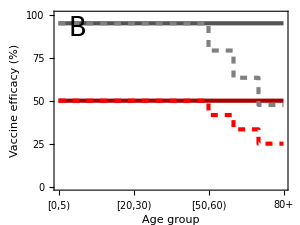

```mathematica
AgeSpecificEfficacyProfile[BaselineValue_]:={{1,BaselineValue},{7,BaselineValue},{7,BaselineValue-(BaselineValue-BaselineValue/2)/3},{8,BaselineValue-(BaselineValue-BaselineValue/2)/3},{8,BaselineValue-2(BaselineValue-BaselineValue/2)/3},{9,BaselineValue-2(BaselineValue-BaselineValue/2)/3},{9,BaselineValue/2},{10,BaselineValue/2}};
ConstantEfficacyProfile[BaselineValue_]:={{1,BaselineValue},{10,BaselineValue}};

ImSize=300;

fig1B=Show[ListLinePlot[{ConstantEfficacyProfile[95],ConstantEfficacyProfile[50],AgeSpecificEfficacyProfile[95],AgeSpecificEfficacyProfile[50]},AspectRatio->0.75,ImageSize->ImSize,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],Darker[Gray]},{Thickness[0.01],Darker[Red]},{Gray,Dashed},{Red,Dashed}},FrameLabel-> {{"Vaccine efficacy (%)",None},{"Age group",None}},PlotTheme-> "Web",PlotRange->{{1,10},{0,100}},PlotRangePadding->None,FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic}],Graphics[Text[StyleForm["B",FontSize->26],Scaled[{0.1,0.9}]]]]

format={".pdf",".eps"};

(*Table[Export[StringJoin["Figures//Fig1B",format⟦i⟧],fig1B],{i,1,Length[format]}];*)
```

## Demography and contact matrices

Imported demography PT 10 age groups

(433332.
461299.
1.05668×10^6
1.09208×10^6
1.25045×10^6
1.57523×10^6
1.48212×10^6
1.2933×10^6
973123.
668660.)

Imported demography PT 17 age groups

(433332.
461299.
507646.
549033.
544575.
547505.
571355.
679093.
792670.
782555.
747581.
734540.
672758.
620543.
544016.
429107.
668660.)

Imported demography NL 10 age groups

(866062.
917442.
2.00833×10^6
2.20179×10^6
2.1082×10^6
2.26111×10^6
2.50839×10^6
2.08991×10^6
1.52211×10^6
798820.)

Imported demography NL 17 age groups

(866062.
917442.
956315.
1.05202×10^6
1.07993×10^6
1.12186×10^6
1.07691×10^6
1.03129×10^6
1.02539×10^6
1.23572×10^6
1.27686×10^6
1.23153×10^6
1.09684×10^6
993074.
913384.
608726.
798820.)

Imported contact matrix PT before the lockdown 16 age groups

(2.5896 | 0.804684 | 0.304764 | 0.21177 | 0.311748 | 0.615214 | 0.939848 | 0.864798 | 0.47479 | 0.25731 | 0.24719 | 0.188627 | 0.14055 | 0.1244 | 0.0854492 | 0.0483542
0.76345 | 4.5649 | 0.888805 | 0.269362 | 0.135034 | 0.411398 | 0.785379 | 0.942651 | 0.821328 | 0.318395 | 0.213586 | 0.165769 | 0.14358 | 0.120167 | 0.061128 | 0.052829
0.167434 | 1.42258 | 7.07196 | 0.767668 | 0.234083 | 0.236325 | 0.401634 | 0.78975 | 1.04906 | 0.499163 | 0.275605 | 0.138829 | 0.0864582 | 0.104991 | 0.0780326 | 0.0733984
0.0953777 | 0.257912 | 2.17437 | 7.37128 | 1.14897 | 0.621134 | 0.544085 | 0.818182 | 0.987631 | 0.876617 | 0.425816 | 0.168308 | 0.0756531 | 0.0589411 | 0.0373322 | 0.0271346
0.153111 | 0.129647 | 0.199075 | 1.74596 | 3.47483 | 1.6302 | 1.19386 | 1.12438 | 0.925029 | 1.00695 | 0.662694 | 0.317464 | 0.101728 | 0.0513646 | 0.0588598 | 0.055928
0.418154 | 0.247953 | 0.141726 | 0.717595 | 1.8876 | 3.5733 | 1.91356 | 1.56081 | 1.29163 | 1.04187 | 0.916881 | 0.429779 | 0.152563 | 0.0675958 | 0.0381027 | 0.0287432
0.635546 | 0.898539 | 0.594943 | 0.457635 | 1.05064 | 1.90297 | 3.42514 | 2.18936 | 1.5449 | 1.1811 | 0.860014 | 0.540441 | 0.246356 | 0.133965 | 0.0759401 | 0.0751264
0.628149 | 1.00728 | 0.895339 | 0.816957 | 0.765681 | 1.50023 | 2.01658 | 3.61005 | 2.21177 | 1.36726 | 0.90663 | 0.466607 | 0.315329 | 0.232461 | 0.147754 | 0.0604242
0.279968 | 0.606867 | 0.895462 | 1.0965 | 0.898423 | 1.28208 | 1.68465 | 1.94117 | 2.96267 | 1.64326 | 1.05812 | 0.353125 | 0.222011 | 0.15623 | 0.113756 | 0.0580184
0.338495 | 0.452543 | 0.550061 | 1.39677 | 0.820247 | 1.0225 | 1.31161 | 1.48116 | 1.54908 | 2.0966 | 1.04924 | 0.425332 | 0.18254 | 0.115189 | 0.108969 | 0.102342
0.209257 | 0.571576 | 0.834232 | 1.11116 | 0.859169 | 1.21903 | 1.20066 | 1.19646 | 1.52288 | 1.65086 | 1.75913 | 0.729923 | 0.289979 | 0.153368 | 0.110392 | 0.101735
0.413513 | 0.605121 | 0.55202 | 0.721731 | 0.578094 | 0.996647 | 1.12372 | 0.93767 | 0.987028 | 0.815126 | 1.01326 | 1.45752 | 0.517769 | 0.265915 | 0.146228 | 0.10414
0.352744 | 0.333317 | 0.232332 | 0.398564 | 0.35842 | 0.568112 | 0.732291 | 0.844741 | 0.639151 | 0.536874 | 0.495201 | 0.699003 | 1.25005 | 0.531536 | 0.30305 | 0.141822
0.229975 | 0.373206 | 0.313438 | 0.182838 | 0.24992 | 0.394536 | 0.659675 | 0.700445 | 0.627883 | 0.400744 | 0.41866 | 0.542889 | 0.648516 | 1.31149 | 0.381853 | 0.19945
0.129054 | 0.343935 | 0.350814 | 0.374042 | 0.175902 | 0.315424 | 0.395009 | 0.727404 | 0.684119 | 0.574224 | 0.417634 | 0.416738 | 0.738973 | 0.871931 | 1.1968 | 0.386836
0.25801 | 0.343299 | 0.506562 | 0.397087 | 0.194396 | 0.221113 | 0.417844 | 0.462229 | 0.521337 | 0.57654 | 0.555067 | 0.375617 | 0.311183 | 0.510464 | 0.460042 | 0.753576)

Imported school contact matrix PT before the lockdown 16 age groups

(1.66051 | 0.26834 | 0.0509724 | 0.0526263 | 0.0123117 | 0.0706302 | 0.15275 | 0.11822 | 0.0521619 | 0.0606281 | 0.0316418 | 0.0206473 | 0.00260088 | 0.00101002 | 8.27936×10^-66 | 6.40828×10^-120
0.335772 | 2.84217 | 0.167469 | 0.0176249 | 0.0144978 | 0.0542965 | 0.0860027 | 0.0861113 | 0.0785907 | 0.0547269 | 0.045465 | 0.0138426 | 0.00526092 | 0.00143012 | 0.000348625 | 8.1182×10^-39
0.00295165 | 0.650166 | 3.99749 | 0.117878 | 0.00971625 | 0.0444741 | 0.05507 | 0.0929602 | 0.0912733 | 0.0699409 | 0.0482956 | 0.023753 | 0.00584671 | 0.0007571 | 4.95596×10^-25 | 0.000182852
0.0168767 | 0.0265016 | 1.18128 | 3.84976 | 0.0380132 | 0.0479371 | 0.0651295 | 0.0970075 | 0.0768016 | 0.0883692 | 0.0480322 | 0.0279311 | 0.00615754 | 0.00109025 | 6.23285×10^-33 | 1.71325×10^-70
0.0165484 | 0.0115921 | 0.0048152 | 0.388773 | 0.216441 | 0.0290088 | 0.0218991 | 0.0278921 | 0.0173487 | 0.0211463 | 0.0113473 | 0.00817789 | 0.000645981 | 0.00121154 | 0.000177231 | 1.22026×10^-47
0.0227918 | 0.0756706 | 0.0249559 | 0.122587 | 0.16068 | 0.119433 | 0.0241917 | 0.033517 | 0.0384517 | 0.0333907 | 0.00870023 | 0.0139604 | 0.00457032 | 0.00245067 | 0.000463795 | 0.00128792
0.0538104 | 0.307111 | 0.213864 | 0.129597 | 0.0329953 | 0.0757203 | 0.0807013 | 0.0587282 | 0.0615074 | 0.031725 | 0.0257134 | 0.00379157 | 0.00645221 | 0.000473418 | 1.65816×10^-48 | 3.11874×10^-55
0.0951461 | 0.192073 | 0.148192 | 0.0716003 | 0.0134611 | 0.0509861 | 0.0836181 | 0.0655822 | 0.070219 | 0.0333104 | 0.00489867 | 0.0109994 | 0.000699282 | 0.00225462 | 1.84907×10^-123 | 9.71935×10^-67
0.0289698 | 0.104091 | 0.0869557 | 0.33298 | 0.00631632 | 0.0246579 | 0.0283427 | 0.040212 | 0.0832557 | 0.0294452 | 0.0326703 | 0.00884886 | 0.00682765 | 0.000514165 | 4.82359×10^-68 | 2.40772×10^-92
0.238478 | 0.229539 | 0.156428 | 0.530003 | 0.00454231 | 0.0304338 | 0.0686509 | 0.062248 | 0.0561085 | 0.0334626 | 0.0409513 | 0.0182493 | 0.00411504 | 0.00182086 | 6.22424×10^-134 | 3.2804×10^-72
0.0576784 | 0.37265 | 0.48982 | 0.497371 | 0.00460442 | 0.0154414 | 0.0500429 | 0.0517281 | 0.0623844 | 0.084589 | 0.042674 | 0.0220929 | 0.00577609 | 9.62647×10^-24 | 1.24075×10^-117 | 5.65431×10^-78
0.171177 | 0.341453 | 0.309723 | 0.334554 | 0.00537945 | 0.0582598 | 0.0258761 | 0.0452734 | 0.0554566 | 0.0399184 | 0.0347616 | 0.0377628 | 0.0109801 | 1.21328×10^-31 | 0.000783335 | 0.000763698
0.0737849 | 0.0657965 | 0.0348462 | 0.156822 | 0.0117186 | 0.00181008 | 0.0184368 | 0.0529987 | 0.0114245 | 0.0180404 | 0.0141459 | 0.00713495 | 0.0233664 | 0.0115642 | 4.42716×10^-67 | 2.12265×10^-37
0.00217706 | 0.0279268 | 0.0110222 | 7.69605×10^-32 | 0.00190096 | 0.00195541 | 0.013152 | 0.00583086 | 0.00582293 | 0.00936293 | 0.00211082 | 0.0159675 | 0.00845152 | 0.0176352 | 0.011127 | 3.45783×10^-126
1.28761×10^-28 | 5.1279×10^-26 | 1.93743×10^-40 | 0.0076306 | 2.63686×10^-22 | 1.69998×10^-24 | 1.26161×10^-26 | 0.00764088 | 0.00786849 | 0.0212029 | 0.0352907 | 0.0214737 | 0.0077468 | 0.00801554 | 0.0079129 | 0.0213827
2.82937×10^-94 | 0.0212049 | 8.49807×10^-42 | 0.0213359 | 4.90075×10^-36 | 0.00760384 | 9.79395×10^-69 | 2.23656×10^-60 | 1.4404×10^-48 | 8.57957×10^-60 | 4.70441×10^-42 | 1.6008×10^-46 | 2.21183×10^-83 | 8.86092×10^-107 | 1.02043×10^-80 | 6.61417×10^-113)

Contact matrix PT before the lockdown 10 age groups

(2.5896 | 0.804684 | 0.516534 | 0.926962 | 1.80465 | 0.7321 | 0.435817 | 0.264949 | 0.133803 | 0.0753485
0.76345 | 4.5649 | 1.15817 | 0.546432 | 1.72803 | 1.13972 | 0.379355 | 0.263747 | 0.113957 | 0.0823213
0.129995 | 0.817437 | 8.72605 | 1.14571 | 1.28017 | 1.71243 | 0.507798 | 0.161908 | 0.106246 | 0.0769165
0.285988 | 0.188959 | 1.40072 | 5.28344 | 2.89786 | 2.13328 | 1.1639 | 0.186716 | 0.0907526 | 0.0659131
0.631529 | 0.957597 | 1.41086 | 2.58013 | 5.62109 | 3.18927 | 1.38567 | 0.47127 | 0.182082 | 0.104625
0.309044 | 0.530201 | 1.96954 | 2.01271 | 3.21197 | 4.12889 | 1.44271 | 0.338244 | 0.191416 | 0.12472
0.310487 | 0.588201 | 1.61252 | 1.82869 | 2.23073 | 2.49398 | 2.48 | 0.612018 | 0.231079 | 0.160387
0.293837 | 0.352457 | 0.566304 | 0.791188 | 1.47295 | 1.1053 | 1.08257 | 1.86719 | 0.510333 | 0.264082
0.185918 | 0.343654 | 0.803696 | 0.457894 | 1.01555 | 1.18758 | 0.876842 | 1.26287 | 1.42047 | 0.854788
0.25801 | 0.343299 | 0.903648 | 0.415509 | 0.880073 | 1.09788 | 0.930684 | 0.821647 | 1.21362 | 1.17427)

Data//CONTACT MATRIX PT BEFORE 10.csv

School contact matrix PT before the lockdown 10 age groups

(1.66051 | 0.26834 | 0.103599 | 0.0829419 | 0.27097 | 0.11279 | 0.0522891 | 0.00361089 | 8.27936×10^-66 | 9.98576×10^-120
0.335772 | 2.84217 | 0.185094 | 0.0687943 | 0.172114 | 0.133318 | 0.0593076 | 0.00669104 | 0.000348625 | 1.26503×10^-38
0.0101869 | 0.32612 | 4.59114 | 0.0706923 | 0.15536 | 0.16327 | 0.0740826 | 0.00693841 | 0.0000878451 | 0.000136885
0.0196785 | 0.0437173 | 0.270236 | 0.262828 | 0.0537606 | 0.0552134 | 0.0210971 | 0.00444618 | 0.000966587 | 0.00100615
0.076259 | 0.244636 | 0.276299 | 0.0846743 | 0.144736 | 0.0988244 | 0.0221153 | 0.00476866 | 7.57646×10^-49 | 2.22054×10^-55
0.133051 | 0.166412 | 0.552328 | 0.0329623 | 0.0995266 | 0.10121 | 0.0503031 | 0.00664338 | 2.42744×10^-68 | 2.53944×10^-72
0.113928 | 0.357188 | 0.817242 | 0.0416507 | 0.0865949 | 0.121401 | 0.0686115 | 0.00835522 | 0.00076671 | 0.000589784
0.0394265 | 0.0476261 | 0.104992 | 0.0088878 | 0.046268 | 0.0226136 | 0.0197442 | 0.0306872 | 0.0053389 | 1.72059×10^-37
7.19829×10^-29 | 0.00935047 | 0.0136741 | 0.00335298 | 0.00427157 | 0.0162521 | 0.0317336 | 0.0088118 | 0.0163774 | 0.0186271
2.82937×10^-94 | 0.0212049 | 0.0213359 | 0.00760384 | 2.23656×10^-60 | 1.4404×10^-48 | 4.70457×10^-42 | 2.21183×10^-83 | 1.02043×10^-80 | 1.03066×10^-112)

Data//SCHOOL CONTACT MATRIX PT BEFORE 10.csv

Imported contact matrix NL before the lockdown 10 age groups

(3.49459 | 1.42731 | 1.26515 | 1.49621 | 1.96756 | 1.43407 | 0.976927 | 0.574687 | 0.198497 | 0.0610699
1.33991 | 7.87519 | 3.51819 | 1.97454 | 2.00887 | 1.87543 | 1.0857 | 0.56934 | 0.235369 | 0.0675934
0.547496 | 1.6218 | 9.37298 | 2.93988 | 1.893 | 2.14217 | 1.4002 | 0.602697 | 0.253254 | 0.100411
0.605267 | 0.850866 | 2.74815 | 4.661 | 2.52761 | 2.17794 | 1.69773 | 0.781362 | 0.338618 | 0.210781
0.837104 | 0.910422 | 1.86105 | 2.65831 | 3.6402 | 2.60697 | 1.72487 | 0.908763 | 0.404453 | 0.239114
0.530857 | 0.739517 | 1.83241 | 1.99297 | 2.26829 | 3.44006 | 1.93336 | 0.952193 | 0.462985 | 0.235091
0.344565 | 0.407904 | 1.1412 | 1.48021 | 1.42995 | 1.84211 | 2.28018 | 1.18511 | 0.54166 | 0.297305
0.240551 | 0.253858 | 0.582957 | 0.808495 | 0.894096 | 1.07671 | 1.40647 | 1.87324 | 0.915692 | 0.385562
0.125495 | 0.158515 | 0.369988 | 0.529201 | 0.601021 | 0.790737 | 0.970935 | 1.38309 | 1.99376 | 0.799441
0.0696997 | 0.0821797 | 0.264826 | 0.594672 | 0.641466 | 0.724839 | 0.962044 | 1.05132 | 1.44327 | 1.18527)

Imported contact matrix NL after the lockdown 10 age groups

(0.911111 | 0.7125 | 1.16247 | 1.0395 | 0.851587 | 0.651538 | 0.453069 | 0.218131 | 0.0792282 | 0.019646
0.672592 | 0.886057 | 1.36309 | 1.14145 | 0.906771 | 0.733406 | 0.517174 | 0.251122 | 0.0999042 | 0.028022
0.501295 | 0.622683 | 1.55959 | 1.28721 | 0.969845 | 0.812777 | 0.606975 | 0.30669 | 0.134222 | 0.0432633
0.408884 | 0.47562 | 1.17411 | 1.50641 | 1.0952 | 0.886122 | 0.699729 | 0.378278 | 0.18436 | 0.070615
0.34984 | 0.39461 | 0.923905 | 1.14381 | 1.29034 | 0.989988 | 0.777751 | 0.455424 | 0.247491 | 0.106761
0.249556 | 0.297582 | 0.72192 | 0.862875 | 0.923039 | 1.11674 | 0.870666 | 0.542549 | 0.326707 | 0.154754
0.156431 | 0.189156 | 0.485971 | 0.614202 | 0.653671 | 0.784835 | 0.961546 | 0.664486 | 0.435074 | 0.220932
0.0903923 | 0.110239 | 0.294715 | 0.398525 | 0.459408 | 0.586992 | 0.797539 | 0.82594 | 0.598574 | 0.317188
0.0450803 | 0.0602167 | 0.177097 | 0.266681 | 0.342786 | 0.485324 | 0.716981 | 0.821863 | 0.868945 | 0.478011
0.0213 | 0.0321833 | 0.10877 | 0.194628 | 0.281751 | 0.438032 | 0.693735 | 0.829841 | 0.910856 | 0.692005)

Ratio of contacts after and before the lockdown NL 10 age groups

(0.26072 | 0.499189 | 0.918835 | 0.694753 | 0.432813 | 0.454329 | 0.46377 | 0.379565 | 0.39914 | 0.321697
0.501967 | 0.112512 | 0.38744 | 0.578082 | 0.451385 | 0.39106 | 0.47635 | 0.441075 | 0.424457 | 0.414567
0.915614 | 0.383947 | 0.166392 | 0.437843 | 0.512333 | 0.379418 | 0.433491 | 0.508863 | 0.529989 | 0.430863
0.675543 | 0.558984 | 0.427235 | 0.323195 | 0.433293 | 0.406863 | 0.412156 | 0.484126 | 0.544447 | 0.335016
0.417917 | 0.433437 | 0.496442 | 0.430278 | 0.354469 | 0.379746 | 0.450905 | 0.501147 | 0.611916 | 0.446486
0.4701 | 0.4024 | 0.393973 | 0.43296 | 0.406931 | 0.324627 | 0.450339 | 0.569789 | 0.705654 | 0.658272
0.453996 | 0.463728 | 0.425843 | 0.414944 | 0.457129 | 0.426053 | 0.421697 | 0.560696 | 0.803223 | 0.743116
0.375771 | 0.434253 | 0.505552 | 0.492922 | 0.513824 | 0.545172 | 0.567048 | 0.440915 | 0.653685 | 0.822664
0.35922 | 0.379879 | 0.478655 | 0.503931 | 0.57034 | 0.613761 | 0.738444 | 0.594222 | 0.435833 | 0.597932
0.305596 | 0.391621 | 0.410724 | 0.327286 | 0.43923 | 0.604317 | 0.721105 | 0.78933 | 0.631104 | 0.583838)

Contact matrix PT after the lockdown 10 age groups

(0.675162 | 0.40169 | 0.474609 | 0.64401 | 0.781074 | 0.332614 | 0.202119 | 0.100565 | 0.0534064 | 0.0242394
0.383227 | 0.513608 | 0.44872 | 0.315882 | 0.780006 | 0.4457 | 0.180706 | 0.116332 | 0.0483698 | 0.0341277
0.119025 | 0.313852 | 1.45195 | 0.501642 | 0.655874 | 0.649725 | 0.220126 | 0.0823892 | 0.0563092 | 0.0331404
0.193197 | 0.105625 | 0.598438 | 1.70759 | 1.25562 | 0.867952 | 0.479708 | 0.0903939 | 0.04941 | 0.0220819
0.263926 | 0.415058 | 0.700409 | 1.11017 | 1.9925 | 1.21111 | 0.624807 | 0.236175 | 0.111419 | 0.0467134
0.145281 | 0.213353 | 0.775946 | 0.871424 | 1.30705 | 1.34035 | 0.649707 | 0.192728 | 0.135073 | 0.0820994
0.14096 | 0.272765 | 0.686682 | 0.758802 | 1.01973 | 1.06257 | 1.04581 | 0.343156 | 0.185608 | 0.119186
0.110416 | 0.153055 | 0.286296 | 0.389994 | 0.756839 | 0.602579 | 0.613871 | 0.823274 | 0.333597 | 0.217251
0.0667855 | 0.130547 | 0.384693 | 0.230747 | 0.579209 | 0.728893 | 0.647498 | 0.750427 | 0.619089 | 0.511105
0.0788469 | 0.134443 | 0.37115 | 0.13599 | 0.386555 | 0.663465 | 0.671121 | 0.648551 | 0.76592 | 0.685582)

Data//CONTACT MATRIX PT AFTER 10.csv

Plotting contact matrices

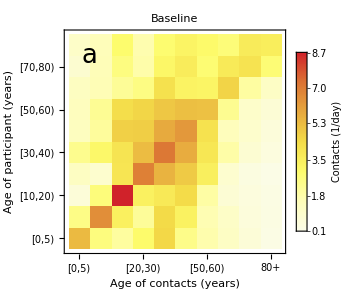

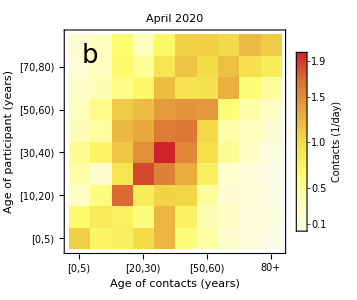

```mathematica
Print[Style["Imported demography PT 10 age groups",18,Blue,"Text"]]
DemographyData10=Flatten[Import["Data//DEMOGRAPHY PT 10.xlsx"]];
DemographyData10//MatrixForm

NumAgeGroups = 10;
AgeGroups= Table[k, {k, 1, NumAgeGroups}];
Demography:=Table[Subscript[NN,k]-> DemographyData10⟦k⟧,{k,AgeGroups}];
AgeLabel={"[0,5) y.o.","[5,10) y.o.","[10,20) y.o.","[20,30) y.o.","[30,40) y.o.","[40,50) y.o.", "[50,60) y.o.","[60,70) y.o.","[70,80) y.o.","80+ y.o."};

AgeLabelShort={"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

Print[Style["Imported demography PT 17 age groups",18,Blue,"Text"]];
DemographyData17=Flatten[Import["Data//DEMOGRAPHY PT 17.xlsx"]];
DemographyData17//MatrixForm

Print[Style["Imported demography NL 10 age groups",18,Blue,"Text"]]
DemographyData10NL=Flatten[Import["Data//DEMOGRAPHY NL 10.xlsx"]];
DemographyData10NL//MatrixForm

Print[Style["Imported demography NL 17 age groups",18,Blue,"Text"]];
DemographyData17NL=Flatten[Import["Data//DEMOGRAPHY NL 17.xlsx"]];
DemographyData17NL//MatrixForm

Print[Style["Imported contact matrix PT before the lockdown 16 age groups",18,Blue,"Text"]];
ContactDataPTBefore16=Import["Data//CONTACT MATRIX PT BEFORE 16.xlsx"]⟦1⟧;
ContactDataPTBefore16//MatrixForm

Print[Style["Imported school contact matrix PT before the lockdown 16 age groups",18,Blue,"Text"]];
SchoolContactDataPTBefore16=Import["Data//SCHOOL CONTACT MATRIX PT BEFORE 16.xlsx"]⟦1⟧;
SchoolContactDataPTBefore16//MatrixForm

(*Print[Style["Function transforming a contact matrix with 16 age groups into a matrix with 10 age groups",18,Blue,"Text"]];*)
MatrixTransform16to10[ContactMatrix16_]:=Block[{ContactMatrix10},
ContactMatrix10=ContactMatrix16;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10]; 

ContactMatrix10=Join[ContactMatrix10,{ContactMatrix10⟦16,All⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Join[ContactMatrix10,List/@(ContactMatrix10⟦All,16⟧ DemographyData17⟦17⟧/DemographyData17⟦16⟧),2] ;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Transpose[{ContactMatrix10⟦All,1⟧,ContactMatrix10⟦All,2⟧,ContactMatrix10⟦All,3⟧+ContactMatrix10⟦All,4⟧,ContactMatrix10⟦All,5⟧+ContactMatrix10⟦All,6⟧,ContactMatrix10⟦All,7⟧+ContactMatrix10⟦All,8⟧,ContactMatrix10⟦All,9⟧+ContactMatrix10⟦All,10⟧,ContactMatrix10⟦All,11⟧+ContactMatrix10⟦All,12⟧,ContactMatrix10⟦All,13⟧+ContactMatrix10⟦All,14⟧,ContactMatrix10⟦All,15⟧+ContactMatrix10⟦All,16⟧,ContactMatrix10⟦All,17⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10={ContactMatrix10⟦1,All⟧,ContactMatrix10⟦2,All⟧,(ContactMatrix10⟦3,All⟧ DemographyData17⟦3⟧+ContactMatrix10⟦4,All⟧ DemographyData17⟦4⟧)/(DemographyData17⟦3⟧+DemographyData17⟦4⟧),(ContactMatrix10⟦5,All⟧ DemographyData17⟦5⟧+ContactMatrix10⟦6,All⟧ DemographyData17⟦6⟧)/(DemographyData17⟦5⟧+DemographyData17⟦6⟧),
(ContactMatrix10⟦7,All⟧ DemographyData17⟦7⟧+ContactMatrix10⟦8,All⟧ DemographyData17⟦8⟧)/(DemographyData17⟦7⟧+DemographyData17⟦8⟧),
(ContactMatrix10⟦9,All⟧ DemographyData17⟦9⟧+ContactMatrix10⟦10,All⟧ DemographyData17⟦10⟧)/(DemographyData17⟦9⟧+DemographyData17⟦10⟧),
(ContactMatrix10⟦11,All⟧ DemographyData17⟦11⟧+ContactMatrix10⟦12,All⟧ DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧),
(ContactMatrix10⟦13,All⟧ DemographyData17⟦13⟧+ContactMatrix10⟦14,All⟧ DemographyData17⟦14⟧)/(DemographyData17⟦13⟧+DemographyData17⟦14⟧),
(ContactMatrix10⟦15,All⟧ DemographyData17⟦15⟧+ContactMatrix10⟦16,All⟧ DemographyData17⟦16⟧)/(DemographyData17⟦15⟧+DemographyData17⟦16⟧),ContactMatrix10⟦17,All⟧};

Dimensions[ContactMatrix10];
ContactMatrix10//MatrixForm;
ContactMatrix10
];

Print[Style["Contact matrix PT before the lockdown 10 age groups",18,Green,"Text"]];
ContactDataPTBefore10=MatrixTransform16to10[ContactDataPTBefore16];
ContactDataPTBefore10//MatrixForm
Export["Data//CONTACT MATRIX PT BEFORE 10.csv",ContactDataPTBefore10,"Table"]

Print[Style["School contact matrix PT before the lockdown 10 age groups",18,Green,"Text"]];
SchoolContactDataPTBefore10=MatrixTransform16to10[SchoolContactDataPTBefore16];
SchoolContactDataPTBefore10//MatrixForm
Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 10.csv",SchoolContactDataPTBefore10,"Table"]

Print[Style["Imported contact matrix NL before the lockdown 10 age groups",18,Blue,"Text"]];
ContactDataNLBefore10=Import["Data//CONTACT MATRIX NL BEFORE 10.csv"];
ContactDataNLBefore10//MatrixForm

Print[Style["Imported contact matrix NL after the lockdown 10 age groups",18,Blue,"Text"]];
ContactDataNLAfter10=Import["Data//CONTACT MATRIX NL AFTER 10.csv"];
ContactDataNLAfter10//MatrixForm

Print[Style["Ratio of contacts after and before the lockdown NL 10 age groups",18,Blue,"Text"]];
RatioContactsAfterAndBeforeNL10=ContactDataNLAfter10/ContactDataNLBefore10;
RatioContactsAfterAndBeforeNL10//MatrixForm

Print[Style["Contact matrix PT after the lockdown 10 age groups",18,Green,"Text"]];
ContactDataPTAfter10=ContactDataPTBefore10 RatioContactsAfterAndBeforeNL10 ;
ContactDataPTAfter10//MatrixForm
Export["Data//CONTACT MATRIX PT AFTER 10.csv",ContactDataPTAfter10,"Table"]

ImSize=300;

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

PlotContactMatrix[matrix_,label_,panel_]:=Show[MatrixPlot[matrix,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{label}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},(*Mesh->True,*)Frame->True,PlotTheme-> "Web",FrameTicks->{{{1,"[0,5)",0},{2,"[5,10)",0},{3,"[10,20)",0},{4,"[20,30)",0},{5,"[30,40)",0},{6,"[40,50)",0},{7,"[50,60)",0},{8,"[60,70)",0},{9,"[70,80)",0},{10,"80+",0}},{{1,Rotate["[0,5)",Pi/2],0},{2,Rotate["[5,10)",Pi/2],0},{3,Rotate["[10,20)",Pi/2],0},{4,Rotate["[20,30)",Pi/2],0},{5,Rotate["[30,40)",Pi/2],0},{6,Rotate["[40,50)",Pi/2],0},{7,Rotate["[50,60)",Pi/2],0},{8,Rotate["[60,70)",Pi/2],0},{9,Rotate["[70,80)",Pi/2],0},{10,Rotate["80+",Pi/2],0}}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14(*,Opacity[1],"Helvetica"*)]],{After,Top}]],Graphics[Text[StyleForm[panel,FontSize->26],{10*0.1,10*0.9}]]]

FigContactMatrixBefore=PlotContactMatrix[ContactDataPTBefore10,"Baseline","a"]
FigContactMatrixAfter=PlotContactMatrix[ContactDataPTAfter10,"April 2020","b"]

format={".pdf",".eps"};
FigNames={"SFig1A","SFig1B"};
Figures={FigContactMatrixBefore,FigContactMatrixAfter};
(*Table[Export[StringJoin["Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]*)
```

## Comparison of contact matrices for PT and NL

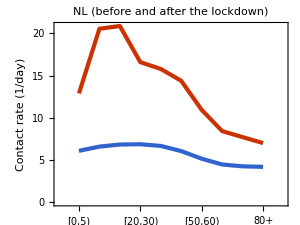

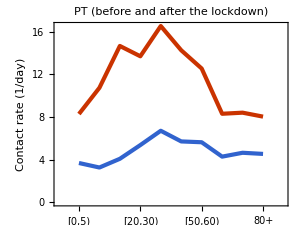

Contact rate before, after and the ratio of the two, PT

{12.1555,5.0685,0.416973}

Contact rate before, after and the ratio of the two, NL

{13.7007,5.79766,0.423164}

```mathematica
CalculateContactsAgeGroups[Matrix10_]:=Table[Total[Matrix10⟦k,All⟧],{k,AgeGroups}];

ContactsAgeGroupsNLBefore=CalculateContactsAgeGroups[ContactDataNLBefore10];
ContactsAgeGroupsPTBefore=CalculateContactsAgeGroups[ContactDataPTBefore10];

ContactsAgeGroupsNLAfter=CalculateContactsAgeGroups[ContactDataNLAfter10];
ContactsAgeGroupsPTAfter=CalculateContactsAgeGroups[ContactDataPTAfter10];

PrintContacts[Before_,After_,Country_]:=ListLinePlot[{Before,After},AspectRatio->0.75,ImageSize->ImSize,PlotRange-> {{0,11},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contact rate (1/day)",None},{None,None}},PlotRange->All,PlotRangePadding->None,PlotTheme-> "Web",PlotLabel->Style[Row[{Country}],Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic}]

PrintContacts[ContactsAgeGroupsNLBefore,ContactsAgeGroupsNLAfter,"NL (before and after the lockdown)"]
PrintContacts[ContactsAgeGroupsPTBefore,ContactsAgeGroupsPTAfter,"PT (before and after the lockdown)"]

CalculateAverageContactRate[Demography_,ContactsAgeGroups_]:=Sum[ContactsAgeGroups⟦k⟧ Demography⟦k⟧/Total[Demography],{k,AgeGroups}];

ContactsPTBeforeTotal=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTBefore];
ContactsPTAfterTotal=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTAfter];

ContactsNLBeforeTotal=CalculateAverageContactRate[DemographyData10NL,ContactsAgeGroupsNLBefore];
ContactsNLAfterTotal=CalculateAverageContactRate[DemographyData10NL,ContactsAgeGroupsNLAfter];

Print[Style["Contact rate before, after and the ratio of the two, PT",18,Blue,"Text"]];
{ContactsPTBeforeTotal,ContactsPTAfterTotal,ContactsPTAfterTotal/ContactsPTBeforeTotal}

Print[Style["Contact rate before, after and the ratio of the two, NL",18,Blue,"Text"]];
{ContactsNLBeforeTotal,ContactsNLAfterTotal,ContactsNLAfterTotal/ContactsNLBeforeTotal}
```

## PT contact matrix by Vespignani et al 85 x 85

Imported demography PT 85 age groups

1.02863×10^7

9.554777×10^6

Imported contact matrix PT before the lockdown 85 age groups

Imported school contact matrix PT before the lockdown 85 age groups

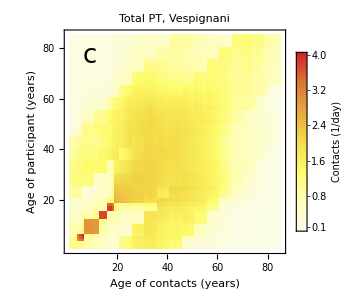

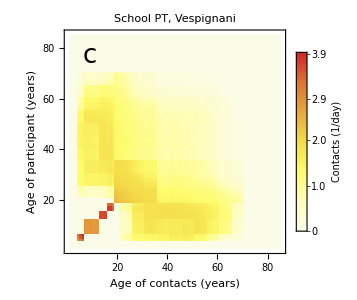

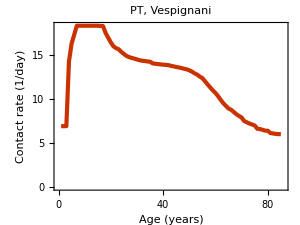

```mathematica
Print[Style["Imported demography PT 85 age groups",18,Blue,"Text"]];
DemographyData85=Import["Data//Portugal_country_level_age_distribution_85.csv"]⟦All,2⟧;
DemographyData85//MatrixForm;

Total[DemographyData10]
Total[DemographyData85]

Print[Style["Imported contact matrix PT before the lockdown 85 age groups",18,Blue,"Text"]];
ContactDataPTBefore85=Import["Data//Portugal_country_level_M_overall_contact_matrix_85.csv"];
ContactDataPTBefore85//MatrixForm;

Print[Style["Imported school contact matrix PT before the lockdown 85 age groups",18,Blue,"Text"]];
SchoolContactDataPTBefore85= 11.41 Import["Data//Portugal_country_level_F_school_setting_85.csv"];
SchoolContactDataPTBefore85//MatrixForm;

Show[MatrixPlot[ContactDataPTBefore85,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{"Total PT, Vespignani"}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->None,Frame->True,PlotTheme-> "Web"(*,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}}*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm["c",FontSize->26],{85*0.1,85*0.9}]]]

Show[MatrixPlot[SchoolContactDataPTBefore85,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{"School PT, Vespignani"}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->None,Frame->True,PlotTheme-> "Web"(*,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}}*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm["c",FontSize->26],{85*0.1,85*0.9}]]]

CalculateContactsAgeGroups2=Table[Total[ContactDataPTBefore85⟦k,All⟧],{k,85}];

ListLinePlot[CalculateContactsAgeGroups2,AspectRatio->0.75,ImageSize->ImSize,PlotRange-> {{0,86},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotTheme-> "Web",FrameLabel-> {{"Contact rate (1/day)",None},{"Age (years)",None}},PlotRange->All,PlotRangePadding->None,PlotLabel->Style[Row[{"PT, Vespignani"}],Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}]
```

## PT contact matrix by Vespignani et al 10 x 10

Data//DEMOGRAPHY PT 86 V.csv

Data//DEMOGRAPHY PT 10 V.csv

Data//CONTACT MATRIX PT BEFORE 86 V.csv

Contact matrix PT before the lockdown 10 age groups Vespignani

(2.54599 | 1.79557 | 0.597741 | 1.58124 | 1.88037 | 0.976327 | 0.37358 | 0.285957 | 0.228345 | 0.158905
1.66701 | 7.00627 | 3.50534 | 1.12103 | 2.02307 | 1.60218 | 0.570874 | 0.30405 | 0.228345 | 0.158905
0.277096 | 1.7503 | 7.92572 | 1.77052 | 2.18543 | 2.00318 | 1.28105 | 0.368414 | 0.243935 | 0.163057
0.591971 | 0.45205 | 1.42984 | 3.86932 | 2.78535 | 2.57546 | 1.94659 | 0.985505 | 0.3383 | 0.187177
0.60404 | 0.699997 | 1.5144 | 2.39 | 2.96178 | 2.49673 | 1.84907 | 1.00521 | 0.525449 | 0.191036
0.341158 | 0.603025 | 1.50995 | 2.40387 | 2.71588 | 2.50389 | 1.81707 | 0.969533 | 0.549773 | 0.408321
0.155063 | 0.255228 | 1.14703 | 2.15821 | 2.38921 | 2.15841 | 1.8196 | 1.19895 | 0.620215 | 0.333587
0.145453 | 0.166582 | 0.404239 | 1.33899 | 1.59168 | 1.41131 | 1.46925 | 1.21007 | 1.00448 | 0.523675
0.144409 | 0.155546 | 0.332783 | 0.571482 | 1.03446 | 0.995011 | 0.944983 | 1.24889 | 1.10364 | 0.869867
0.144409 | 0.155546 | 0.319654 | 0.454369 | 0.540446 | 1.06194 | 0.730372 | 0.935621 | 1.24999 | 0.979677)

Data//CONTACT MATRIX PT BEFORE 10 V.csv

Contact matrix PT after the lockdown 10 age groups Vespignani

(0.66379 | 0.896331 | 0.549225 | 1.09857 | 0.813849 | 0.443574 | 0.173255 | 0.108539 | 0.0911416 | 0.0511191
0.836786 | 0.788293 | 1.35811 | 0.648049 | 0.913181 | 0.626547 | 0.271936 | 0.134109 | 0.0969225 | 0.0658767
0.253713 | 0.672021 | 1.31878 | 0.775213 | 1.11967 | 0.760043 | 0.555326 | 0.187472 | 0.129283 | 0.070255
0.399902 | 0.252689 | 0.610879 | 1.25055 | 1.20687 | 1.04786 | 0.802298 | 0.477108 | 0.184186 | 0.0627074
0.252438 | 0.303404 | 0.751813 | 1.02836 | 1.04986 | 0.948123 | 0.833753 | 0.50376 | 0.321531 | 0.0852948
0.160378 | 0.242657 | 0.594879 | 1.04078 | 1.10517 | 0.81283 | 0.818297 | 0.552429 | 0.38795 | 0.268786
0.0703978 | 0.118356 | 0.488453 | 0.895535 | 1.09218 | 0.919597 | 0.76732 | 0.672245 | 0.498172 | 0.247894
0.0546569 | 0.0723389 | 0.204364 | 0.660016 | 0.817845 | 0.769406 | 0.833138 | 0.533537 | 0.656613 | 0.430808
0.0518747 | 0.0590889 | 0.159288 | 0.287988 | 0.589993 | 0.610699 | 0.697817 | 0.74212 | 0.481003 | 0.520121
0.044131 | 0.0609153 | 0.131289 | 0.148709 | 0.23738 | 0.641748 | 0.526675 | 0.738514 | 0.788875 | 0.571973)

Data//CONTACT MATRIX PT AFTER 10 V.csv

School contact matrix PT before the lockdown 10 age groups Vespignani

Data//SCHOOL CONTACT MATRIX PT BEFORE 86 V.csv

(1.94146 | 1.29028 | 0. | 0.0253809 | 0.0592522 | 0.0914605 | 0.0256729 | 0.00205149 | 0. | 0.
1.1979 | 6.37547 | 2.70494 | 0.104617 | 0.287726 | 0.286894 | 0.22302 | 0.0201486 | 0. | 0.
0. | 1.35064 | 6.80854 | 0.924351 | 0.487979 | 0.356924 | 0.222397 | 0.0313604 | 0. | 0.
0.00950192 | 0.0421863 | 0.746488 | 1.42563 | 0.246543 | 0.0608675 | 0.0355611 | 0.0120944 | 0. | 0.
0.0190338 | 0.0995556 | 0.338147 | 0.211549 | 0.0497481 | 0.0220656 | 0.0135955 | 0.00271788 | 0. | 0.
0.0319591 | 0.107981 | 0.269041 | 0.0568123 | 0.0240024 | 0.0167527 | 0.0104474 | 0.0014702 | 0. | 0.
0.0106561 | 0.0997085 | 0.199129 | 0.0394271 | 0.0175669 | 0.01241 | 0.00829965 | 0.00111587 | 0. | 0.
0.00104349 | 0.011039 | 0.0344099 | 0.0164324 | 0.00430357 | 0.00214012 | 0.00136745 | 0.00023978 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Data//SCHOOL CONTACT MATRIX PT BEFORE 10 V.csv

Plotting contact matrices

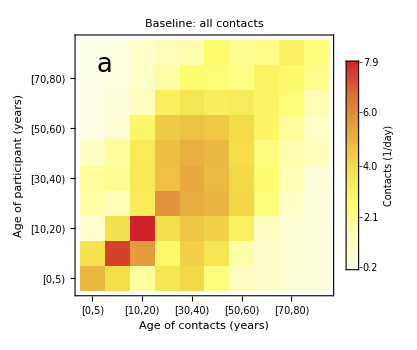
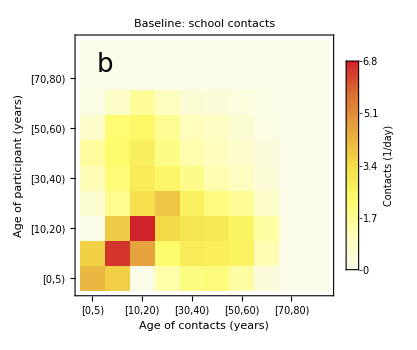
-Graphics- | -Graphics-

{Figures//SFig2.pdf,Figures//SFig2.eps}

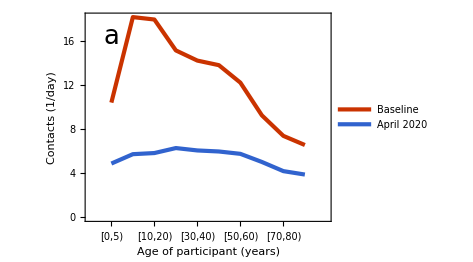
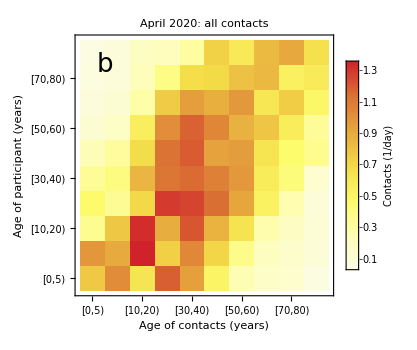
-Graphics- | -Graphics-

{Figures//SFig3.pdf,Figures//SFig3.eps}

{13.0301,5.58024,0.428258}

```mathematica
ListTransform86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
(*Demography10Test= Join[Partition[Range[0,85],5]⟦1;;2⟧,Partition[Range[0,85],10]⟦2;;⟧,{Range[0,85]⟦81;;⟧}];*)

(* https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
DemographyData86=Append[DemographyData85,316442];
DemographyData10Vespignani=ListTransform86to10[DemographyData86];

Export["Data//DEMOGRAPHY PT 86 V.csv",DemographyData86,"Table"]

Export["Data//DEMOGRAPHY PT 10 V.csv",DemographyData10Vespignani,"Table"]

(* Join[{v},m]//MatrixForm - join a row v to matrix m
Join[List/@v,m,2]//MatrixForm - join a column v to matrix m *)

ContactDataPTBefore86x85=Join[ContactDataPTBefore85,{ContactDataPTBefore85⟦85⟧}];
(*ContactDataPTBefore86x85//Dimensions
ContactDataPTBefore86x85//MatrixForm*)
ContactDataPTBefore86x86=Join[ContactDataPTBefore86x85,List/@(ContactDataPTBefore86x85⟦All,85⟧ DemographyData86⟦86⟧/DemographyData86⟦85⟧), 2];
(*ContactDataPTBefore86x86//Dimensions
ContactDataPTBefore86x86//MatrixForm*)
Export["Data//CONTACT MATRIX PT BEFORE 86 V.csv",ContactDataPTBefore86x86,"Table"]


Print[Style["Contact matrix PT before the lockdown 10 age groups Vespignani",18,Red,"Text"]];
ContactDataPTBefore10Vespignani=ListTransform86to10[ Transpose[ListTransform86to10[Transpose[ContactDataPTBefore86x86]]] DemographyData86]/DemographyData10Vespignani;
ContactDataPTBefore10Vespignani//MatrixForm
Export["Data//CONTACT MATRIX PT BEFORE 10 V.csv",ContactDataPTBefore10Vespignani,"Table"]

Print[Style["Contact matrix PT after the lockdown 10 age groups Vespignani",18,Red,"Text"]];
ContactDataPTAfter10Vespignani=ContactDataPTBefore10Vespignani RatioContactsAfterAndBeforeNL10 ;
ContactDataPTAfter10Vespignani//MatrixForm
Export["Data//CONTACT MATRIX PT AFTER 10 V.csv",ContactDataPTAfter10Vespignani,"Table"]

Print[Style["School contact matrix PT before the lockdown 10 age groups Vespignani",18,Red,"Text"]];

SchoolContactDataPTBefore86x85=Join[SchoolContactDataPTBefore85,{SchoolContactDataPTBefore85⟦85⟧}];
(*SchoolContactDataPTBefore86x85//Dimensions
SchoolContactDataPTBefore86x85//MatrixForm*)
SchoolContactDataPTBefore86x86=Join[SchoolContactDataPTBefore86x85,List/@(SchoolContactDataPTBefore86x85⟦All,85⟧ DemographyData86⟦86⟧/DemographyData86⟦85⟧), 2];
(*ContactDataPTBefore86x86//Dimensions
ContactDataPTBefore86x86//MatrixForm*)
Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 86 V.csv",SchoolContactDataPTBefore86x86,"Table"]

SchoolContactDataPTBefore10Vespignani=ListTransform86to10[ Transpose[ListTransform86to10[Transpose[SchoolContactDataPTBefore86x86]]] DemographyData86]/DemographyData10Vespignani;
SchoolContactDataPTBefore10Vespignani//MatrixForm
Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 10 V.csv",SchoolContactDataPTBefore10Vespignani,"Table"]

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

FigContactMatrixBeforeV=PlotContactMatrix[ContactDataPTBefore10Vespignani,"Baseline: all contacts","a"];
FigContactMatrixAfterV=PlotContactMatrix[ContactDataPTAfter10Vespignani,"April 2020: all contacts","b"];
FigSchoolContactMatrixBeforeV=PlotContactMatrix[SchoolContactDataPTBefore10Vespignani,"Baseline: school contacts","b"];

format={".pdf",".eps"};
FigNames={"SFig1A","SFig1B","SFig1C"};
Figures={FigContactMatrixBeforeV,FigSchoolContactMatrixBeforeV,FigContactMatrixAfterV};
(*Table[Export[StringJoin["Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]*)

BeforeAfterLegends=Style[#,Black]&/@{"Baseline","April 2020"};

PrintContactsPaper[Before_,After_]:=Show[ListLinePlot[{Before,After},AspectRatio->0.75,ImageSize->350,PlotRange-> {{0,11},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contacts (1/day)",None},{"Age of participant (years)",None}},PlotRange->All,PlotRangePadding->None,PlotTheme-> "Web"(*,PlotLabel->Style[Row[{Country}],Black,17]*),FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic},PlotLegends->Placed[BeforeAfterLegends,Scaled[{{1,1}, {1,1 }}]],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,30}}],Graphics[Text[StyleForm["a",FontSize->26],{10*0.1,Max[Before]*0.9}]]]


ContactsAgeGroupsPTBeforeV=CalculateContactsAgeGroups[ContactDataPTBefore10Vespignani];
ContactsAgeGroupsPTAfterV=CalculateContactsAgeGroups[ContactDataPTAfter10Vespignani];

FigBeforeAfter=PrintContactsPaper[ContactsAgeGroupsPTBeforeV,ContactsAgeGroupsPTAfterV];

SFig2=Grid[{{FigContactMatrixBeforeV,FigSchoolContactMatrixBeforeV}}]
Table[Export[StringJoin["Figures//SFig2",format⟦i⟧],SFig2],{i,1,Length[format]}]

SFig3=Grid[{{FigBeforeAfter,FigContactMatrixAfterV}}]
Table[Export[StringJoin["Figures//SFig3",format⟦i⟧],SFig3],{i,1,Length[format]}]

ContactsPTBeforeTotalV=CalculateAverageContactRate[DemographyData10Vespignani,ContactsAgeGroupsPTBeforeV];
ContactsPTAfterTotalV=CalculateAverageContactRate[DemographyData10Vespignani,ContactsAgeGroupsPTAfterV];
{ContactsPTBeforeTotalV,ContactsPTAfterTotalV,ContactsPTAfterTotalV/ContactsPTBeforeTotalV}
```

## Serological data

```mathematica
(* 
Grupo etário (anos)
1-9 
10-19 
20-39
40-59
≥60 
*)
```

```mathematica
TotalSamples5={404,377,377,479,664};

Total[TotalSamples5]

PositivePecentage5={2.9,2.2,2.9,3.2,2.9}/100;

Round[TotalSamples5 PositivePecentage5]

SamplesTransform5to10[Variable5_]:=Round[{Variable5⟦1⟧ DemographyData17⟦1⟧/(DemographyData17⟦1⟧+DemographyData17⟦2⟧),Variable5⟦1⟧ DemographyData17⟦2⟧/(DemographyData17⟦1⟧+DemographyData17⟦2⟧),Variable5⟦2⟧,Variable5⟦3⟧ DemographyData10⟦4⟧/(DemographyData10⟦4⟧+DemographyData10⟦5⟧),Variable5⟦3⟧ DemographyData10⟦5⟧/(DemographyData10⟦4⟧+DemographyData10⟦5⟧),Variable5⟦4⟧ DemographyData10⟦6⟧/(DemographyData10⟦6⟧+DemographyData10⟦7⟧),Variable5⟦4⟧ DemographyData10⟦7⟧/(DemographyData10⟦6⟧+DemographyData10⟦7⟧),Variable5⟦5⟧ DemographyData10⟦8⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧),Variable5⟦5⟧ DemographyData10⟦9⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧),Variable5⟦5⟧ DemographyData10⟦10⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧)}];

SamplesTransform5to10[TotalSamples5]

SamplesTransform5to10[TotalSamples5 PositivePecentage5]
```

2301

{12,8,11,15,19}

{196,208,377,176,201,247,232,293,220,151}

{6,6,8,5,6,8,7,8,6,4}

## Important dates

```mathematica
Print[Style["Important dates",18,Blue,"Text"]]
Print[Style["Date of starting simulations",18,Blue,"Text"]]
DateObject[{2020, 02, 25}]
t0=0

Print[Style["Date of the start of the pandemic",18,Blue,"Text"]]
DateObject[{2020, 02, 26}]

Print[Style["Date of starting vaccination",18,Blue,"Text"]]
(*tstartvac=255;*)
DateObject[{2020, 12, 27}]
tstartvac=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 12, 27}]}]⟦1,1⟧+1

Print[Style["Date of ending vaccination",18,Blue,"Text"]]
(*DateObject[{2021, 07, 31}]*)
DateObject[{2021, 12, 31}]
tendvac=Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,12,31}](*DateObject[{2021, 07, 31}]*)}]⟦1,1⟧+1+10 (*days extra*) (* DateObject[{2021, 12, 31}] *)

Print[Style["Last hospitalization date",18,Blue,"Text"]]

tenddata=254 (* 5 Nov but starting with t=1 *)
```

Important dates

Date of starting simulations

Tue 25 Feb 2020

0

Date of the start of the pandemic

Wed 26 Feb 2020

Date of starting vaccination

Sun 27 Dec 2020

306

Date of ending vaccination

Fri 31 Dec 2021

685

Last hospitalization date

254

## Vaccination plan

```mathematica
Categories={{"Profissionais de saúde","Profissionais e residentes em ERPI e RNCCI","50+ com insuficiência cardíaca","50+ com doença coronária","50+ com insuficiência renal","50+ com DPOC ou doença respiratória crónica","Profissionais das forças de segurança e da Proteção Civil"},{"65+ com ou sem patologias","Entre os 50 e os 64 anos com diabetes","Entre os 50 e os 64 anos com neoplasia maligna ativa","Entre os 50 e os 64 anos com insuficiência hepática","Entre os 50 e os 64 anos com doença renal crónica","Entre os 50 e os 64 anos com obesidade","Entre os 50 e os 64 anos com hipertensão arterial"},{"Restante população"}};

Fase1=1;
Fase2=2;
Fase3=3;

Print[Style["Categories: phase 1",18,Blue,"Text"]];
Categories⟦Fase1⟧
Print[Style["Categories: phase 2",18,Blue,"Text"]];
Categories⟦Fase2⟧
Print[Style["Categories: phase 3",18,Blue,"Text"]];
Categories⟦Fase3⟧

NumberOfCategories={Length[Categories⟦Fase1⟧],Length[Categories⟦Fase2⟧],Length[Categories⟦Fase3⟧]};

Print[Style["Number of categories: phase 1",18,Blue,"Text"]];
NumberOfCategories⟦Fase1⟧
Print[Style["Number of categories: phase 2",18,Blue,"Text"]];
NumberOfCategories⟦Fase2⟧
Print[Style["Number of categories: phase 3",18,Blue,"Text"]];
NumberOfCategories⟦Fase3⟧

PersonsToVaccinate={{199708,148119,207571,169265,8201,128597,75900},{1873349,222864,114246,93004,4222,392959,632547},{6529448}};

Print[Style["Persons to vaccinate per category: phase 1",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase1⟧
Print[Style["Persons to vaccinate per category: phase 2",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase2⟧
Print[Style["Persons to vaccinate per category: phase 3",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase3⟧


Print[Style["Total: phase 1",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]
Print[Style["Total: phase 2",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase2⟧]
Print[Style["Total: phase 3",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase3⟧]
Print[Style["Total: phase 1 and phase 2",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]+Total[PersonsToVaccinate⟦Fase2⟧]
Print[Style["Total: all phases",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]+Total[PersonsToVaccinate⟦Fase2⟧]+Total[PersonsToVaccinate⟦Fase3⟧]

Print[Style["Start and end vaccination dates: all phases",18,Blue,"Text"]];
StartAndEndVaccinationDates={{
{DateObject[{2020, 12, 27}],DateObject[{2021, 02, 28}]},
{DateObject[{2021, 01, 01}],DateObject[{2021, 02, 28}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]}},

{{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]}},

{DateObject[{2021, 08, 01}],DateObject[{2021, 12, 31}]}};

Print[Style["Start and end vaccination dates: phase 1",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase1⟧
Print[Style["Start and end vaccination dates: phase 2",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase2⟧
Print[Style["Start and end vaccination dates: phase 3",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase3⟧

Print[Style["Duration of vaccination per category (days): phase 1",18,Blue,"Text"]];
Duration1=Flatten[Map[Differences,StartAndEndVaccinationDates⟦Fase1⟧]]⟦All,1⟧
Print[Style["Duration of vaccination per category (days): phase 2",18,Blue,"Text"]];
Duration2=Flatten[Map[Differences,StartAndEndVaccinationDates⟦Fase2⟧]]⟦All,1⟧
Print[Style["Duration of vaccination per category (days): phase 3",18,Blue,"Text"]];
Duration3=Differences[StartAndEndVaccinationDates⟦Fase3⟧]⟦All,1⟧

Print[Style["Duration of vaccination per category (days): all phases",18,Blue,"Text"]];
DurationVaccination={Duration1,Duration2,Duration3}

Print[Style["Start vaccination dates: phase 1",18,Blue,"Text"]];
StartVaccinationDates1=Subscript[t, vaccination]+ Prepend[Flatten[Map[Differences,Table[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase1⟧⟦cat,1⟧},{cat,2,Length[StartAndEndVaccinationDates⟦Fase1⟧]}]]]⟦All,1⟧,0]


Print[Style["Start vaccination dates: phase 2",18,Blue,"Text"]];
StartVaccinationDates2=Subscript[t, vaccination]+ Flatten[Map[Differences,Table[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase2⟧⟦cat,1⟧},{cat,1,Length[StartAndEndVaccinationDates⟦Fase2⟧]}]]]⟦All,1⟧


Print[Style["Start vaccination dates: phase 3",18,Blue,"Text"]];
StartVaccinationDates3=Subscript[t, vaccination]+Differences[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase3⟧⟦1⟧}]⟦All,1⟧

Print[Style["Start vaccination dates: all phases",18,Blue,"Text"]];
StartVaccinationDates={StartVaccinationDates1,StartVaccinationDates2,StartVaccinationDates3}

Print[Style["End vaccination dates: all phases",18,Blue,"Text"]];
EndVaccinationDates=StartVaccinationDates+DurationVaccination

Print[Style["Total vaccination rate r = ∑ r_k",18,Blue,"Text"]];
Print[Style["Persons to vaccinate per day for each category and phase",18,Blue,"Text"]];
TotalVacRate=PersonsToVaccinate/DurationVaccination//N
```

Categories: phase 1

{Profissionais de saúde,Profissionais e residentes em ERPI e RNCCI,50+ com insuficiência cardíaca,50+ com doença coronária,50+ com insuficiência renal,50+ com DPOC ou doença respiratória crónica,Profissionais das forças de segurança e da Proteção Civil}

Categories: phase 2

{65+ com ou sem patologias,Entre os 50 e os 64 anos com diabetes,Entre os 50 e os 64 anos com neoplasia maligna ativa,Entre os 50 e os 64 anos com insuficiência hepática,Entre os 50 e os 64 anos com doença renal crónica,Entre os 50 e os 64 anos com obesidade,Entre os 50 e os 64 anos com hipertensão arterial}

Categories: phase 3

{Restante população}

Number of categories: phase 1

7

Number of categories: phase 2

7

Number of categories: phase 3

1

Persons to vaccinate per category: phase 1

{199708,148119,207571,169265,8201,128597,75900}

Persons to vaccinate per category: phase 2

{1873349,222864,114246,93004,4222,392959,632547}

Persons to vaccinate per category: phase 3

{6529448}

Total: phase 1

937361

Total: phase 2

3333191

Total: phase 3

6529448

Total: phase 1 and phase 2

4270552

Total: all phases

10800000

Start and end vaccination dates: all phases

Start and end vaccination dates: phase 1

{{Sun 27 Dec 2020,Sun 28 Feb 2021},{Fri 1 Jan 2021,Sun 28 Feb 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021}}

Start and end vaccination dates: phase 2

{{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021}}

Start and end vaccination dates: phase 3

{Sun 1 Aug 2021,Fri 31 Dec 2021}

Duration of vaccination per category (days): phase 1

{63,58,88,88,88,88,88}

Duration of vaccination per category (days): phase 2

{91,91,91,91,91,91,91}

Duration of vaccination per category (days): phase 3

{152}

Duration of vaccination per category (days): all phases

{{63,58,88,88,88,88,88},{91,91,91,91,91,91,91},{152}}

Start vaccination dates: phase 1

{t_vaccination,5+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination}

Start vaccination dates: phase 2

{125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination}

Start vaccination dates: phase 3

{217+t_vaccination}

Start vaccination dates: all phases

{{t_vaccination,5+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination},{125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination},{217+t_vaccination}}

End vaccination dates: all phases

{{63+t_vaccination,63+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination},{216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination},{369+t_vaccination}}

Total vaccination rate r = ∑ r_k

Persons to vaccinate per day for each category and phase

{{3169.97,2553.78,2358.76,1923.47,93.1932,1461.33,862.5},{20586.3,2449.05,1255.45,1022.02,46.3956,4318.23,6951.07},{42956.9}}

## Vaccination rates

Binary vector of vaccination ages per category
{0-4,5-9,10-19,20-29,30-39,40-49,50-59,60-69,70-79,80+}
Format:1-yes,vaccinate this age group,0-no,do not vaccinate this age group
NB! To vaccinate e.g.60-64 age group,include a correction

```mathematica
Print[Style["Vaccination rates r_k",18,Blue,"Text"]];
Print[Style["Persons to vaccinate per day in each age group",18,Blue,"Text"]];

VacRate[Category_,VaccinationAges_,Correction_,Demography_,TotalVacRate_]:=Block[{PersonsToVaccinate,AgeDistributionVaccination},

Print[Style[Category,18,Red,"Text"]];

(* Persons to vaccinate in different age groups *)

PersonsToVaccinate=VaccinationAges Correction Demography;

(* Age distribution for vaccinations *)

AgeDistributionVaccination=PersonsToVaccinate/Total[PersonsToVaccinate];

TotalVacRate AgeDistributionVaccination
]

R11=VacRate[Categories⟦1,1⟧,{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,1⟧]

R12a=VacRate["Profissionais em ERPI e RNCCI",{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,2⟧ 0.8 (60991+15431)/PersonsToVaccinate⟦Fase1⟧⟦2⟧]

R12b=VacRate["Residentes em ERPI e RNCCI",{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,27500 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),27500 (DemographyData17⟦15⟧+DemographyData17⟦16⟧)/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),82500},TotalVacRate⟦1,2⟧ 0.8 (99234+9493)/PersonsToVaccinate⟦Fase1⟧⟦2⟧]

Print[Style["Profissionais e residentes em ERPI e RNCCI",18,Red,"Text"]];
R12=R12a+R12b

ImportPersonsToVaccinate[column_]:=Reverse[Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧⟦5;;15,column⟧];
PersonsToVaccinate11to10[Vector_]:={0,0,0,0,0,0,Vector⟦1⟧+Vector⟦2⟧,Vector⟦3⟧+Vector⟦4⟧,Vector⟦5⟧+Vector⟦6⟧,Total[Vector⟦7;;11⟧]};

InsuficienciaCardiaca=PersonsToVaccinate11to10[ImportPersonsToVaccinate[5]];
R13=VacRate[Categories⟦1,3⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},InsuficienciaCardiaca,TotalVacRate⟦1,3⟧]
(*Total[InsuficienciaCardiaca] 
PersonsToVaccinate⟦Fase1⟧⟦3⟧*)

DoencaCoronaria=PersonsToVaccinate11to10[ImportPersonsToVaccinate[8]];
R14=VacRate[Categories⟦1,4⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},DoencaCoronaria,TotalVacRate⟦1,4⟧]

(* 65-75: 3361
75+:4840 *)

InsuficienciaRenal={0,0,0,0,0,0,0,3361 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧),3361 DemographyData17⟦15⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧)+4840 DemographyData17⟦16⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧),4840 DemographyData17⟦17⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧)};

R15=VacRate[Categories⟦1,5⟧,{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},InsuficienciaRenal,TotalVacRate⟦1,5⟧]

DoencaRespiratoriaCronica=PersonsToVaccinate11to10[ImportPersonsToVaccinate[14]];
R16=VacRate[Categories⟦1,6⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},DoencaRespiratoriaCronica,TotalVacRate⟦1,6⟧]

R17=VacRate[Categories⟦1,7⟧,{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,7⟧]

Print[Style["Vector of vaccination rates: phase 1",18,Blue,"Text"]];
VacRatesVector1={R11,R12,R13,R14,R15,R16, R17}

R21=VacRate[Categories⟦2,1⟧,{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1, DemographyData17⟦14⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦2,1⟧]

ImportPersonsToVaccinate50to65[column_]:=Reverse[Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧⟦13;;15,column⟧];
PersonsToVaccinate3to10[Vector_]:={0,0,0,0,0,0,Vector⟦1⟧+Vector⟦2⟧,Vector⟦3⟧,0,0};

Diabetes=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[11]];
R22=VacRate[Categories⟦2,2⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},Diabetes,TotalVacRate⟦2,2⟧]

NeoplasiaMaligna=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[23]];
R23=VacRate[Categories⟦2,3⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},NeoplasiaMaligna,TotalVacRate⟦2,3⟧]

InsuficienciaHepatica=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[29]];
R24=VacRate[Categories⟦2,4⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},InsuficienciaHepatica,TotalVacRate⟦2,4⟧]

DoencaRenalCronica={0,0,0,0,0,0,4222 (DemographyData17⟦11⟧+DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧+DemographyData17⟦13⟧),4222 DemographyData17⟦13⟧/(DemographyData17⟦11⟧+DemographyData17⟦12⟧+DemographyData17⟦13⟧),0,0};
R25=VacRate[Categories⟦2,5⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},DoencaRenalCronica,TotalVacRate⟦2,5⟧]

Obesidade=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[20]];
R26=VacRate[Categories⟦2,6⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},Obesidade,TotalVacRate⟦2,6⟧]

HipertensaoArterial=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[17]];
R27=VacRate[Categories⟦2,7⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},HipertensaoArterial,TotalVacRate⟦2,7⟧]

Print[Style["Vector of vaccination rates: phase 2",18,Blue,"Text"]];
VacRatesVector2={R21,R22,R23,R24,R25,R26,R27}

Print[Style["Restante população",18,Red,"Text"]];
R31=VacRate[Categories⟦3,1⟧,{0,0,0,1 ,1 ,1 ,1 ,0 ,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦3,1⟧]

(*R31⟦4;;7⟧=R31⟦4;;7⟧ {0.8,0.9,1,0.5}*)

(*R31={0,0,0,0,0,0,0,0,0,0}*)

Print[Style["Vector of vaccination rates: phase 3",18,Blue,"Text"]];
VacRatesVector3={R31}

Print[Style["Vector of vaccination rates: all phases",18,Blue,"Text"]];
VacRatesVector={VacRatesVector1,VacRatesVector2,VacRatesVector3}
```

Vaccination rates r_k

Persons to vaccinate per day in each age group

Profissionais de saúde

{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.}

Profissionais em ERPI e RNCCI

{0.,0.,0.,189.565,217.055,273.43,257.269,116.778,0.,0.}

Residentes em ERPI e RNCCI

{0.,0.,0.,0.,0.,0.,0.,145.987,228.934,1124.76}

Profissionais e residentes em ERPI e RNCCI

{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76}

50+ com insuficiência cardíaca

{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58}

50+ com doença coronária

{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455}

50+ com insuficiência renal

{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501}

50+ com DPOC ou doença respiratória crónica

{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932}

Profissionais das forças de segurança e da Proteção Civil

{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}

Vector of vaccination rates: phase 1

{{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.},{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76},{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58},{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455},{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501},{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932},{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}}

65+ com ou sem patologias

{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54}

Entre os 50 e os 64 anos com diabetes

{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.}

Entre os 50 e os 64 anos com neoplasia maligna ativa

{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.}

Entre os 50 e os 64 anos com insuficiência hepática

{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.}

Entre os 50 e os 64 anos com doença renal crónica

{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.}

Entre os 50 e os 64 anos com obesidade

{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.}

Entre os 50 e os 64 anos com hipertensão arterial

{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}

Vector of vaccination rates: phase 2

{{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54},{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.},{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.},{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.},{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.},{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.},{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}}

Restante população

Restante população

{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}

Vector of vaccination rates: phase 3

{{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}}

Vector of vaccination rates: all phases

{{{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.},{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76},{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58},{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455},{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501},{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932},{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54},{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.},{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.},{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.},{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.},{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.},{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}},{{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}}}

## Age distribution of vaccination categories

The coordinates of Scaled are :
{{Position on graphic in x, Position on graphic in y}, {Part of plot legend that should be at the assigned position on graphic}}
{{0.9, 0.9}, {1, 1}} assigns a location on my graphic 90 % up the graphic and 90 % to the right, and puts the upper right corner of my plot legend at this point
{{0.5, 0.5}, {0.5, 0.5}} puts the middle of my plot legend in the middle of my graphic

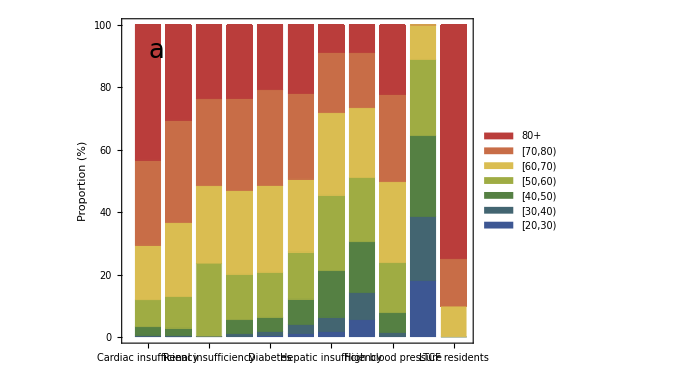
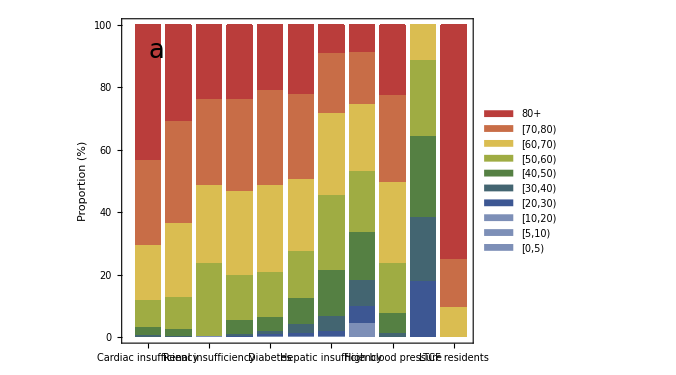

```mathematica
CategoriesAgeDistribution=Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧;
ImportCategoriesAgeDistribution[i_]:=Join[{Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦1⟧+Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦2⟧,Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦3⟧},Total/@Partition[Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦4;;17⟧,2],{Total[Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦18;;22⟧]}];

A11=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];
A12a=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];
(*A12b=Join[{0,0,0,0,0,0,0,DemographyData17⟦14⟧},DemographyData10⟦9;;10⟧];*)

A12b={0,0,0,0,0,0,0,27500 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),27500 (DemographyData17⟦15⟧+DemographyData17⟦16⟧)/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),82500};

A13=ImportCategoriesAgeDistribution[5];
A14=ImportCategoriesAgeDistribution[8];
A15={72 DemographyData17⟦1⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],72 DemographyData17⟦2⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],72 (DemographyData17⟦3⟧+DemographyData17⟦4⟧)/Sum[DemographyData17⟦i⟧,{i,1,5}],72 DemographyData17⟦5⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],0,0,4222 (DemographyData17⟦11⟧+DemographyData17⟦12⟧)/Sum[DemographyData17⟦i⟧,{i,11,13}],4222 DemographyData17⟦13⟧/Sum[DemographyData17⟦i⟧,{i,11,13}]+3361 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧),3361 DemographyData17⟦15⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧)+4840 DemographyData17⟦16⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧),4840 DemographyData17⟦17⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧)};
(*Manuel said that the 20-65 are all in the 50-65 age groups*)
A16=ImportCategoriesAgeDistribution[14];
A17=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];

A22=ImportCategoriesAgeDistribution[11];
A23=ImportCategoriesAgeDistribution[23];
A24=ImportCategoriesAgeDistribution[29];
(* A25 Same disease as A15 so I grouped them *)
A26=ImportCategoriesAgeDistribution[20];
A27=ImportCategoriesAgeDistribution[17];

BarChartFormat[x_]:=100 x/Total[x];

AgeDistributionChartLabel={"Cardiac insufficiency","Coronary heart disease","Renal insufficiency", "Chronic respiratory disease","Diabetes","Neoplasm","Hepatic insufficiency","Obesity","High blood pressure","HCW, LTCF staff, Police","LTCF residents"};

BarChartLegends=Style[#,Black]&/@{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

ChartStyleColors=Join[{Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]](*ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0]*)},ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;7⟧]];

AspRat=0.75;

PlotBarChart[StartAgeGroup_,colors_]:=Show[BarChart[BarChartFormat/@(#⟦StartAgeGroup;;⟧&/@{A13,A14,A15,A16,A22,A23,A24,A26,A27,A11,A12b}),ChartLayout->"Stacked",ImageSize->500,ChartLabels->{Rotate[Style[#,Black,14],Pi/2]&/@AgeDistributionChartLabel,None},ChartLegends->Placed[BarChartLegends⟦StartAgeGroup;;⟧,(*{After,Top}*){Scaled[ {{1.1, 0.5}, {0.5,0.5 }}]}], PlotTheme->"Web",Joined->False,BarSpacing->0.2,AspectRatio->AspRat,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],ChartStyle->colors,FrameLabel-> {{"Proportion (%)",None},{None,None}},PlotRange->{All,{0,100}},PlotRangePadding->None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.1,0.9}]]]]

{PlotBarChart[4,"DarkRainbow"],fig1A=PlotBarChart[1,ChartStyleColors]}

format={".pdf",".eps"};

(*Table[Export[StringJoin["Figures//Fig1A",format⟦i⟧],fig1A],{i,1,Length[format]}];*)
```

## Vaccination rates as piece-wise functions

```mathematica
Clear[CreatePiecewiseRate,Rates,UnconstrainedRates,OrderIntervals]

CreatePiecewiseRate[Rate_,StartVaccinationDate_,EndVaccinationDate_]:=
Piecewise[{{0,t<0},{0,Subscript[t, start]≤t<StartVaccinationDate},{Rate,StartVaccinationDate≤t≤EndVaccinationDate},{0,t> EndVaccinationDate}}]/.{Subscript[t, vaccination]->tstartvac,Subscript[t, start]-> t0}

UnconstrainedRates=Table[ PiecewiseExpand[Sum[Sum[CreatePiecewiseRate[VacRatesVector⟦Fase⟧⟦Category⟧⟦k⟧,StartVaccinationDates⟦Fase⟧⟦Category⟧,EndVaccinationDates⟦Fase⟧⟦Category⟧],{Category,1,NumberOfCategories⟦Fase⟧}],
{Fase,{Fase1,Fase2,Fase3}}]],{k,AgeGroups}];
Print[Style["Vaccination rates with unordered intervals and without constraints on the number of vaccines",18,Blue,"Text"]]
Rates=UnconstrainedRates

PiecewiseDomains[HoldPattern[Piecewise[cases_,default_]]]:=Module[{dl=Last/@cases},Append[dl,Not[Or@@dl]]]
OrderIntervals=Table[Quiet@Maximize[{t,#},t]&/@PiecewiseDomains[UnconstrainedRates⟦k⟧]//N//Ordering,{k,AgeGroups}];
Table[Rates⟦k⟧⟦1⟧=Table[UnconstrainedRates⟦k⟧⟦1⟧⟦PosInt⟧,{PosInt,OrderIntervals⟦k⟧⟦1;;Length[OrderIntervals⟦k⟧]-1⟧}],{k,AgeGroups}];

Print[Style["Vaccination rates with ordered intervals but without constraints on the number of vaccines",18,Blue,"Text"]];
Rates

Table[Rates⟦k⟧⟦1⟧=Table[{Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦1⟧,Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦2⟧&&Sum[Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦1⟧ (Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦2⟧⟦5⟧-Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦2⟧⟦1⟧),{PosIntSum,1,PosInt-1}]+Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦1⟧ (t-Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦2⟧⟦1⟧)≤0.9 Subscript[NN, k]/.Demography//Simplify},{PosInt,1,Length[Rates⟦k⟧⟦1⟧]}],{k,AgeGroups}];

Print[Style["Vaccination rates with constraints on the number of vaccines",18,Blue,"Text"]];
Table[Rates⟦k⟧=Subscript[r,k]->Rates⟦k⟧,{k,AgeGroups}]
```

Vaccination rates with unordered intervals and without constraints on the number of vaccines

{Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {155.109, 369<t≤430}, {570.076, 306≤t<311}, {759.64, 311≤t<342}, {914.749, 342≤t≤369}, {8687.68, 523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {177.602, 369<t≤430}, {652.745, 306≤t<311}, {869.8, 311≤t<342}, {1047.4, 342≤t≤369}, {9947.52, 523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {223.73, 369<t≤430}, {822.282, 306≤t<311}, {1095.71, 311≤t<342}, {1319.44, 342≤t≤369}, {12531.2, 523≤t≤675}, {0, True}}],Piecewise[{{773.68, 306≤t<311}, {844.984, 369<t≤430}, {1030.95, 311≤t<342}, {1875.93, 342≤t≤369}, {9518.87, 431≤t≤522}, {11790.5, 523≤t≤675}, {0, True}}],Piecewise[{{0., 523≤t≤675}, {351.186, 306≤t<311}, {613.951, 311≤t<342}, {1429.86, 369<t≤430}, {2043.81, 342≤t≤369}, {12170., 431≤t≤522}, {0, True}}],Piecewise[{{0., 306≤t<311||523≤t≤675}, {228.934, 311≤t<342}, {1811.5, 369<t≤430}, {2040.43, 342≤t≤369}, {8855.03, 431≤t≤522}, {0, True}}],Piecewise[{{0., 306≤t<311||523≤t≤675}, {1124.76, 311≤t<342}, {2056.47, 369<t≤430}, {3181.23, 342≤t≤369}, {6084.54, 431≤t≤522}, {0, True}}]}

Vaccination rates with ordered intervals but without constraints on the number of vaccines

{Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{570.076, 306≤t<311}, {759.64, 311≤t<342}, {914.749, 342≤t≤369}, {155.109, 369<t≤430}, {0., 431≤t≤522}, {8687.68, 523≤t≤675}, {0, True}}],Piecewise[{{652.745, 306≤t<311}, {869.8, 311≤t<342}, {1047.4, 342≤t≤369}, {177.602, 369<t≤430}, {0., 431≤t≤522}, {9947.52, 523≤t≤675}, {0, True}}],Piecewise[{{822.282, 306≤t<311}, {1095.71, 311≤t<342}, {1319.44, 342≤t≤369}, {223.73, 369<t≤430}, {0., 431≤t≤522}, {12531.2, 523≤t≤675}, {0, True}}],Piecewise[{{773.68, 306≤t<311}, {1030.95, 311≤t<342}, {1875.93, 342≤t≤369}, {844.984, 369<t≤430}, {9518.87, 431≤t≤522}, {11790.5, 523≤t≤675}, {0, True}}],Piecewise[{{351.186, 306≤t<311}, {613.951, 311≤t<342}, {2043.81, 342≤t≤369}, {1429.86, 369<t≤430}, {12170., 431≤t≤522}, {0., 523≤t≤675}, {0, True}}],Piecewise[{{228.934, 311≤t<342}, {2040.43, 342≤t≤369}, {1811.5, 369<t≤430}, {8855.03, 431≤t≤522}, {0., 306≤t<311||523≤t≤675}, {0, True}}],Piecewise[{{1124.76, 311≤t<342}, {3181.23, 342≤t≤369}, {2056.47, 369<t≤430}, {6084.54, 431≤t≤522}, {0., 306≤t<311||523≤t≤675}, {0, True}}]}

Vaccination rates with constraints on the number of vaccines

{r_1→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_2→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_3→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_4→Piecewise[{{570.076, 306.≤t<311.}, {759.64, 311.≤t<342.}, {914.749, 342.≤t≤369.}, {155.109, 369.<t≤430.}, {0., 431≤t≤522}, {8687.68, 523.≤t≤629.163}, {0, True}}],r_5→Piecewise[{{652.745, 306.≤t<311.}, {869.8, 311.≤t<342.}, {1047.4, 342.≤t≤369.}, {177.602, 369.<t≤430.}, {0., 431≤t≤522}, {9947.52, 523.≤t≤629.163}, {0, True}}],r_6→Piecewise[{{822.282, 306.≤t<311.}, {1095.71, 311.≤t<342.}, {1319.44, 342.≤t≤369.}, {223.73, 369.<t≤430.}, {0., 431≤t≤522}, {12531.2, 523.≤t≤629.163}, {0, True}}],r_7→Piecewise[{{773.68, 306.≤t<311.}, {1030.95, 311.≤t<342.}, {1875.93, 342.≤t≤369.}, {844.984, 369.<t≤430.}, {9518.87, 431.≤t≤522.}, {11790.5, 523.≤t≤550.961}, {0, True}}],r_8→Piecewise[{{351.186, 306.≤t<311.}, {613.951, 311.≤t<342.}, {2043.81, 342.≤t≤369.}, {1429.86, 369.<t≤430.}, {12170., 431.≤t≤513.233}, {0, True}}],r_9→Piecewise[{{228.934, 311.≤t<342.}, {2040.43, 342.≤t≤369.}, {1811.5, 369.<t≤430.}, {8855.03, 431.≤t≤510.404}, {0, True}}],r_10→Piecewise[{{1124.76, 311.≤t<342.}, {3181.23, 342.≤t≤369.}, {2056.47, 369.<t≤430.}, {6084.54, 431.≤t≤489.441}, {0, True}}]}

## Plotting vaccination rates

Vaccination rate (persons per day) for each age group

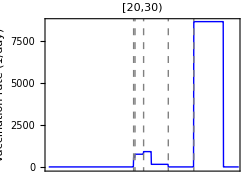
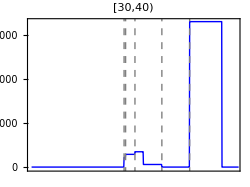
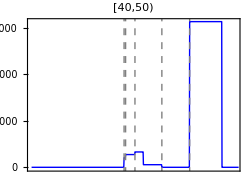
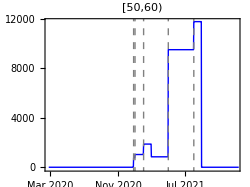
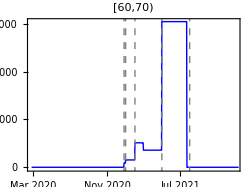
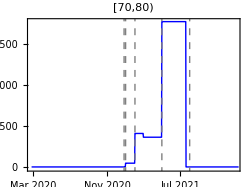
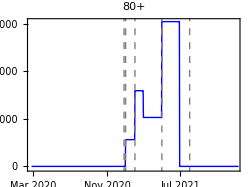
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

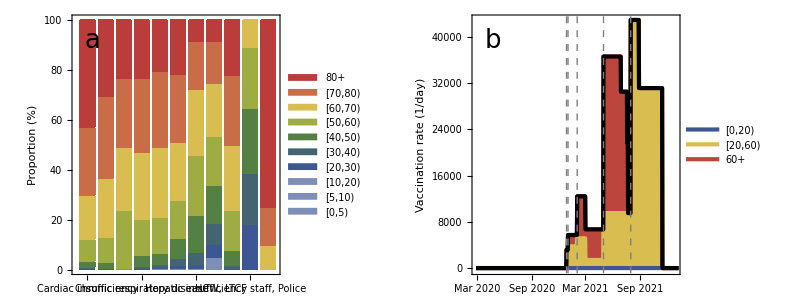

```mathematica
Subscript[t, start]=t0;
Subscript[t, end]=tendvac;

AspRat=0.75; ImSize=350;

FigNames={"A","B","C","D","E","F","G","H","I","J"};
PanelLetter[AgeGroup_]:=Graphics[Text[StyleForm[FigNames⟦AgeGroup⟧,FontSize->26],Scaled[{0.9,0.9}]]];

UniqueStartVaccinationDates=DeleteDuplicates[Join[StartAndEndVaccinationDates⟦1⟧⟦All,1⟧,StartAndEndVaccinationDates⟦2⟧⟦All,1⟧,{StartAndEndVaccinationDates⟦3⟧⟦1⟧}]];
UniqueStartVaccinationDays=DeleteDuplicates[Flatten[StartVaccinationDates]]/.Subscript[t, vaccination]->tstartvac;


VaccinationLines:=Table[DateListPlot[{{UniqueStartVaccinationDates⟦i⟧,0},{UniqueStartVaccinationDates⟦i⟧,10000}},PlotStyle->{Dashed,Gray},DateTicksFormat->{"MonthShort","/","YearShort"}],{i,1,Length[UniqueStartVaccinationDates]}];

Print[Style["Vaccination rate (persons per day) for each age group",24,Blue,"Text"]];

tickValues=DateRange[{2020,3,1},{2022,1,1},{4,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

SFig4=Table[Show[DateListPlot[Table[Rates⟦k,2⟧,{t,Subscript[t, start],Subscript[t, end]}],"February 25, 2020",PlotRange->{{"February 25, 2020","January 01, 2022"},{-75,All}},ImageSize->250,PlotRangePadding->None,
PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,14],Frame-> {{True,False},{True,False}},FrameTicks->{{Automatic,None},{If[k≥ 7,ticks,None],None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)FrameLabel-> {{If[k==4||k==7,"Vaccination rate (1/day)",None],None},{None,None}},Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Filling->None,PlotStyle->{Blue,Thick},PlotLabel->Style[Row[{AgeLabelShort⟦k⟧}],Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{If[k==4||k== 7,65,42], Automatic}, {Automatic, Automatic}}](*,Graphics[Text[StyleForm[FigNames⟦k⟧,FontSize->26],Scaled[{0.9,0.9}]]]*)],{k,Range[4,10]}];
SFig4all=Grid[{SFig4⟦1;;3⟧,SFig4⟦4;;7⟧}]

Table[Export[StringJoin["Figures//SFig4",format⟦i⟧],SFig4all],{i,1,Length[format]}];

VaccinationRatesPlot=Table[Table[Rates⟦k,2⟧,{t,Subscript[t, start],Subscript[t, end]}],{k,AgeGroups}];
VaccinationRatesLegends=Style[#,Black]&/@{"[0,20)","[20,60)","60+"};
lineColors=Part[(ColorData["DarkRainbow"]/@Rescale[{1,2,3,4,5,6,7,8,9,10}]),{1,7,9}];

(*lineColors=ColorData["DarkRainbow"]/@Rescale[{1,2,3}];*)
lineWidths={Thickness[0.01],Thickness[0.01],Thickness[0.01]};

ListLinePlot[{Total[VaccinationRatesPlot⟦1;;3⟧],Total[VaccinationRatesPlot⟦1;;7⟧],Total[VaccinationRatesPlot⟦1;;10⟧]},PlotRange->All,ImageSize->ImSize,PlotLegends->VaccinationRatesLegends,Filling->{3-> {2},2-> {1},1-> Axis},PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameLabel-> {{"Vaccination rate\n(1/day)",None},{"Days",None}},PlotStyle->Transpose[{lineColors,lineWidths}],AxesOrigin->{0,0},PlotRangePadding->None];

tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

fig1B=Show[DateListPlot[{Total[VaccinationRatesPlot⟦1;;3⟧],Total[VaccinationRatesPlot⟦1;;7⟧],Total[VaccinationRatesPlot⟦1;;10⟧]},"February 25, 2020",PlotRange->{{"February 25, 2020","January 01, 2022"},{-250,All}},ImageSize->500,PlotLegends->Placed[VaccinationRatesLegends,Scaled[{{0.1, 0.7}, {0,1 }}]],Filling->{3-> {{2},lineColors⟦3⟧},2-> {{1},lineColors⟦2⟧},1-> Axis},PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)FrameLabel-> {{"Vaccination rate (1/day)",None},{None,None}},Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotStyle->lineColors(*Transpose[{lineColors,lineWidths}]*),AxesOrigin->{0,0},PlotRangePadding->None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{80, Automatic}, {140, Automatic}}],DateListPlot[Total[VaccinationRatesPlot⟦1;;10⟧],"February 25, 2020",PlotStyle->{Black},PlotTheme->"Web"],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.1,0.9}]]]];

(*Table[Export[StringJoin["Figures//Fig1B",format⟦i⟧],fig1B],{i,1,Length[format]}];*)

DateListPlot[Table[Total[VaccinationRatesPlot⟦1;;k⟧],{k,AgeGroups}],"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},PlotRange->All,ImageSize->500,PlotLegends->(Style[#,Black,17]&/@AgeLabel)(*,Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*),Filling->Table[If[k≤ 9,(k+1)-> {k}],{k,AgeGroups}],PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameLabel-> {{"Vaccination rate (1/day)",None},{None,None}},PlotStyle->"CMYKColors",AxesOrigin->{0,0},PlotRangePadding->None];

(*fig1=Grid[{{fig1A},{fig1B}}]*)
fig1=Grid[{{fig1A,fig1B}}]

Table[Export[StringJoin["Figures//Fig1",format⟦i⟧],fig1],{i,1,Length[format]}];
```

## Importing hospitalization data and parameter estimates

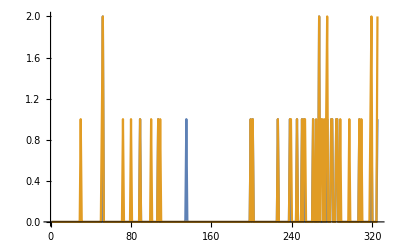
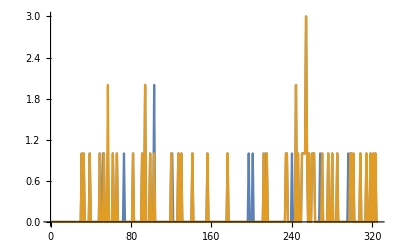
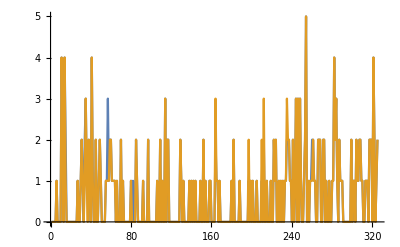
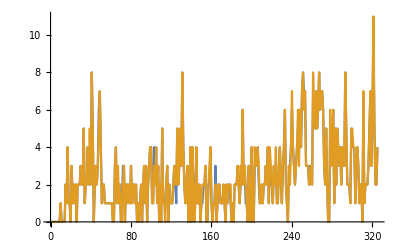
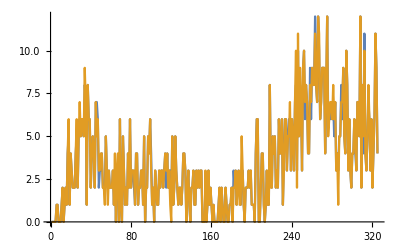
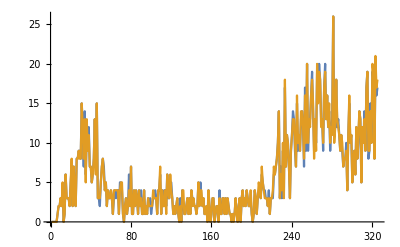
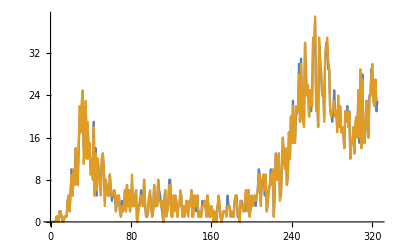
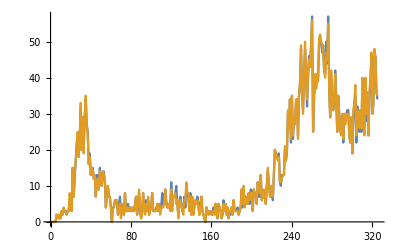

```mathematica
HospitalisationsData=Import["Data//hospitalisations_selected PT updated.csv"];
HospitalisationsData=Drop[HospitalisationsData,1];
Total[Total[HospitalisationsData]];
Dimensions[HospitalisationsData];
TableForm[HospitalisationsData];

HospitalisationsDataNew=Import["Data//hospitalisations_selected PT 15 Jan 2021 2.csv"];
HospitalisationsDataNew=Drop[HospitalisationsDataNew,1];
Total[Total[HospitalisationsDataNew]];
Dimensions[HospitalisationsDataNew];
TableForm[HospitalisationsDataNew];


HospitalisationsDataNew2=Import["Data//hospitalisations_selected PT 15 Jan 2021 3.csv"];
HospitalisationsDataNew2=Drop[HospitalisationsDataNew2,1];
Total[Total[HospitalisationsDataNew2]];
Dimensions[HospitalisationsDataNew2];
TableForm[HospitalisationsDataNew2];

Table[ListLinePlot[{(*HospitalisationsData⟦All,k⟧, *)HospitalisationsDataNew⟦All,k⟧,HospitalisationsDataNew2⟦All,k⟧},PlotRange-> All],{k,AgeGroups}]
```

```mathematica
Total[Total[HospitalisationsDataNew2]]
```

28482

```mathematica
(*Transpose[Insert[Transpose[a],column,2]]*)

HospitalisationsData=Import["Data//hospitalisations_selected PT updated.csv"](*⟦1;;255,All⟧*);
HospitalisationsData=Drop[HospitalisationsData,1];
Dimensions[HospitalisationsData];
TableForm[HospitalisationsData];

ContactRates:=
Flatten[Table[{Subscript[c,{k,l}]->ContactDataPTBefore10Vespignani⟦k,l⟧,Subscript[d,{k,l}]->ContactDataPTAfter10Vespignani⟦k,l⟧,Subscript[s,{k,l}]->SchoolContactDataPTBefore10Vespignani⟦k,l⟧},{k,1,NumAgeGroups},{l,1,NumAgeGroups}]];

Print[Style["Imported estimated parameters",18,Blue,"Text"]]
(*EstimatesData=Import["Data//fit_19012021_PT.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_187days.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days_2.csv"];*)
EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days_corrected_prior_omegaV_beta_std_02_constant_alpha_gamma_sero_classes.csv"];

EstimatesData=Transpose[Insert[Transpose[EstimatesData],Table[gamma,{i,1,Dimensions[EstimatesData]⟦1⟧}],3]];
EstimatesData=Transpose[Insert[Transpose[EstimatesData],Table[alpha,{i,1,Dimensions[EstimatesData]⟦1⟧}],27]]

Print[Style["Dimensions of the imported data",18,Blue,"Text"]]
Dimensions[EstimatesData]

Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderParameters=EstimatesData⟦1⟧

EstimatesData=Drop[EstimatesData,1];

(*DischargeRate:=δ->1/5;*)

(*https://bmcmedicine.biomedcentral.com/articles/10.1186/s12916-020-01726-3*)

ProbTransm[sample_]:=ϵ->EstimatesData⟦sample,1⟧;
zeta[sample_]:=Subscript[ζ, 1]-> EstimatesData⟦sample,2⟧;
LatRate[sample_]:=α->0.4(*EstimatesData⟦sample,27⟧*);
RecRate[sample_]:=γ->0.25(*EstimatesData⟦sample,3⟧*);

(* hosp_classes=c(1,1,1,2,3,4,5,6,7,8) *)
(* susc_classes=c(1,1,1,2,2,2,2,3,3,3) *)

nu[sample_]:=Table[Subscript[ν,k]->EstimatesData⟦sample,3+k⟧,{k,1,10}];

Inoculum[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-EstimatesData⟦sample,14⟧,Subscript[EE0,k]-> 0.5 EstimatesData⟦sample,14⟧,Subscript[II0,k]-> 0.5 EstimatesData⟦sample,14⟧,Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,AgeGroups}]];

Susceptibility[sample_]:=Flatten[Join[Table[Subscript[β,k]->EstimatesData⟦sample,28⟧ ,{k,1,3}],Table[Subscript[β,k]->EstimatesData⟦sample,29⟧ ,{k,4,7}],Table[Subscript[β,k]->EstimatesData⟦sample,30⟧ ,{k,8,10}]]]

x0logfact[sample_]:=x0-> EstimatesData⟦sample,25⟧; 
k0logfact[sample_]:=K0-> EstimatesData⟦sample,26⟧;

RelaxationFraction[sample_]:=u-> EstimatesData⟦sample,32⟧; 
x1logfact[sample_]:=x1-> EstimatesData⟦sample,33⟧; 
k1logfact[sample_]:=K1-> EstimatesData⟦sample,34⟧;

rOverDisp[sample_]:=EstimatesData⟦sample,31⟧;

PropSchoolContacts[sample_]:=Subscript[ζ, 2]->EstimatesData⟦sample,35⟧;
x2logfact[sample_]:=x2-> EstimatesData⟦sample,37⟧; 
k2logfact[sample_]:=K2-> EstimatesData⟦sample,36⟧;

RelaxationProbReduction[sample_]:=Subscript[ζ, 3]-> EstimatesData⟦sample,38⟧;

Parameters[sample_]:=
Flatten[{(*DischargeRate,*)ContactRates,ProbTransm[sample],LatRate[sample],RecRate[sample],nu[sample],Inoculum[sample],zeta[sample],Demography,Susceptibility[sample],x0logfact[sample],k0logfact[sample],x1logfact[sample],k1logfact[sample],RelaxationFraction[sample],PropSchoolContacts[sample],x2logfact[sample],k2logfact[sample],RelaxationProbReduction[sample]}];

VaccineEfficacy[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]:={Subscript[ω, 1]->x1,Subscript[ω, 2]->x2,Subscript[ω, 3]->x3,Subscript[ω, 4]->x4,Subscript[ω, 5]->x5,Subscript[ω, 6]->x6,Subscript[ω, 7]->x7,Subscript[ω, 8]->x8,Subscript[ω, 9]->x9,Subscript[ω, 10]->x10};

VacEffHigh=VaccineEfficacy[0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95];
VacEffLow=VaccineEfficacy[0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5];
```

Imported estimated parameters

{{epsilon,zeta,gamma,nu_short[1],nu_short[2],nu_short[3],nu_short[4],nu_short[5],nu_short[6],nu_short[7],nu_short[8],nu_short[9],nu_short[10],inoculum,p_short[1],p_short[2],p_short[3],p_short[4],p_short[5],p_short[6],p_short[7],p_short[8],p_short[9],p_short[10],x0,k0,alpha,beta_short[1],beta_short[2],beta_short[3],r,u,x1,k1,omega,k2,x2,kappa},249,{0.0636154,0.76838,gamma,0.0026093,0.000558313,29,0.493963,1.07663,175.728,0.670657}}
 |  |  |  |

Dimensions of the imported data

{251,38}

Header of the imported data

{epsilon,zeta,gamma,nu_short[1],nu_short[2],nu_short[3],nu_short[4],nu_short[5],nu_short[6],nu_short[7],nu_short[8],nu_short[9],nu_short[10],inoculum,p_short[1],p_short[2],p_short[3],p_short[4],p_short[5],p_short[6],p_short[7],p_short[8],p_short[9],p_short[10],x0,k0,alpha,beta_short[1],beta_short[2],beta_short[3],r,u,x1,k1,omega,k2,x2,kappa}

## Parameters vector

```mathematica
ParametersMAP=Parameters[200];

NumSamples=Dimensions[EstimatesData]⟦1⟧;

ParametersMAPNoVaccination=Join[ParametersMAP,Table[Subscript[r,k]-> 0,{k,AgeGroups}]];
ParametersMAPVaccination=Join[ParametersMAP,Rates,VacEffHigh];

ParametersNoVaccination[sample_]:=Join[Parameters[sample],Table[Subscript[r,k]-> 0,{k,AgeGroups}]];
ParametersVaccination[sample_]:=Join[Parameters[sample],Rates,VacEffHigh];
(*ParametersVaccinationL[sample_]:=Join[Parameters[sample],Rates,VacEffLow];*)
```

## Plotting parameter estimates

{{Probability of transmission per contact, ϵ,0.0635078,0.0544456,0.0742424},{Reduction in probability of
transmission per contact (lockdown), (1-ζ_1),0.233895,0.175189,0.305624},{Initial fraction of infected persons, θ,0.000148765,0.000105656,0.000202761},{Susceptibility of [0,20) y.o. relative to 60+ y.o., β_([0, 20)),0.313056,0.238366,0.433048},{Susceptibility of [20,60) y.o. relative to 60+ y.o., β_([20, 60)),0.624321,0.504324,0.778538},{Midpoint value of the logistic function (days), t_1,29.7712,28.4278,30.9068},{Logistic growth rate (1/day), K_1,0.755825,0.31664,3.95479},{Overdispersion parameter, r,19.2633,15.0009,26.2424},{Midpoint value of the 2nd logistic function (days), t_2,60.7808,58.3997,63.509},{2nd logistic growth rate (1/day), K_2,1.63974,0.464021,4.62882},{Proportion of contacts during relaxation, u,0.24547,0.214225,0.281914},{Reduction in probability of
transmission per contact at schools, (1-ζ_2),0.548887,0.39374,0.666709},{Midpoint value of the school logistic function (days), t_3,178.857,175.352,182.129},{School logistic growth rate (1/day), K_3,1.69252,1.02204,4.94035},{Reduction in probability of
transmission per contact (relaxation), (1-ζ_3),0.334932,0.294635,0.377378}}

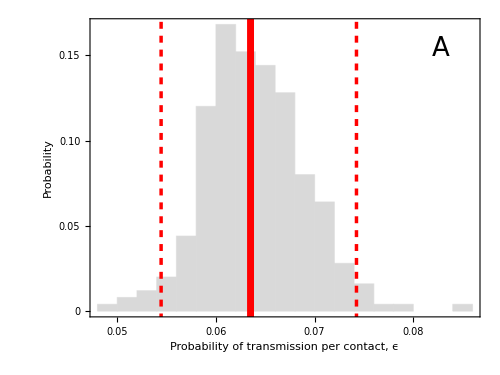
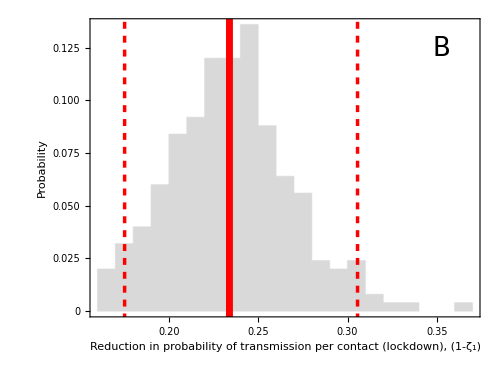
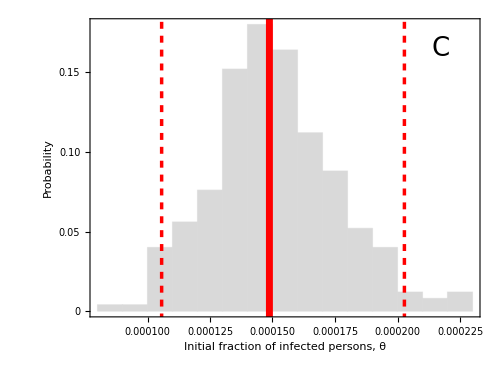
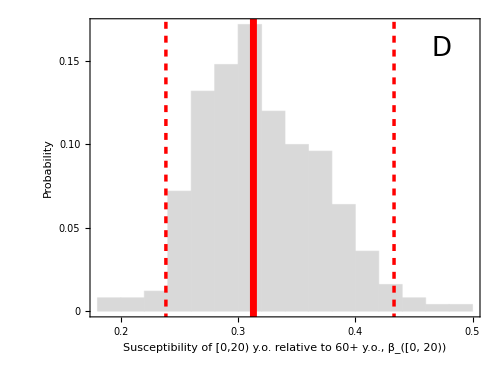
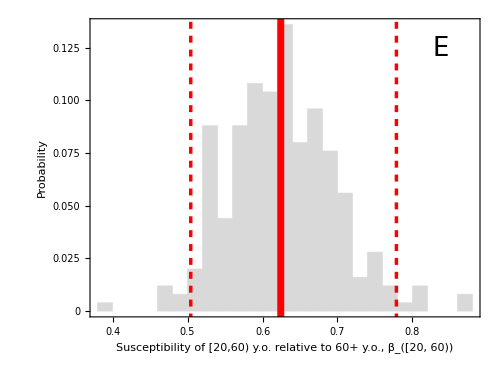
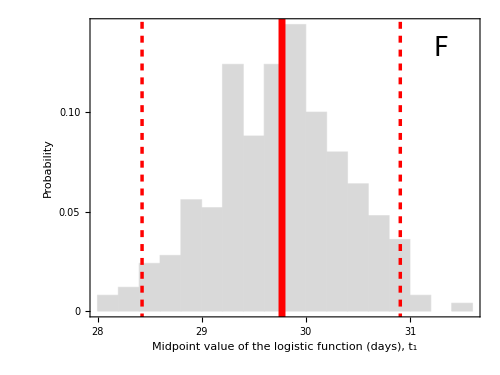
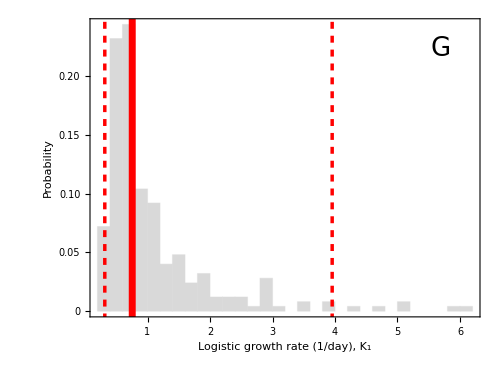
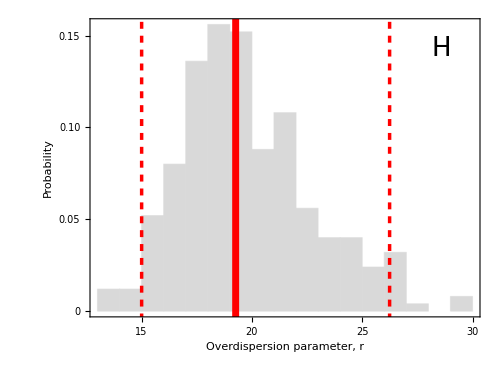

```mathematica
AspRat=0.75; ImSize=400;

HistPlot[vals_,xlab_,panel_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->500,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray],Graphics[{Thickness[0.01],Red,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}],Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]]

(*InfiniteLine[{StartVaccinationDates⟦i⟧,0},{0,1}]*)

vals={EstimatesData⟦All,1⟧,(*1/EstimatesData⟦All,27⟧,*)(1-EstimatesData⟦All,2⟧),(*1/EstimatesData⟦All,3⟧,*)EstimatesData⟦All,14⟧,EstimatesData⟦All,28⟧,EstimatesData⟦All,29⟧,EstimatesData⟦All,25⟧,EstimatesData⟦All,26⟧,EstimatesData⟦All,31⟧,EstimatesData⟦All,33⟧,EstimatesData⟦All,34⟧,EstimatesData⟦All,32⟧, (1-EstimatesData⟦All,35⟧), EstimatesData⟦All,37⟧, EstimatesData⟦All,36⟧,(1-EstimatesData⟦All,38⟧)};

xlab={"Probability of transmission per contact, ϵ",(*"Latent period (days), 1/α",*)"Reduction in probability of\ntransmission per contact (lockdown), (1-ζ_1)",(*"Infectious period (days), 1/γ",*)"Initial fraction of infected persons, θ","Susceptibility of [0,20) y.o. relative to 60+ y.o., β_([0, 20))","Susceptibility of [20,60) y.o. relative to 60+ y.o., β_([20, 60))","Midpoint value of the logistic function (days), t_1","Logistic growth rate (1/day), K_1","Overdispersion parameter, r","Midpoint value of the 2nd logistic function (days), t_2","2nd logistic growth rate (1/day), K_2","Proportion of contacts during relaxation, u","Reduction in probability of\ntransmission per contact at schools, (1-ζ_2)","Midpoint value of the school logistic function (days), t_3","School logistic growth rate (1/day), K_3","Reduction in probability of\ntransmission per contact (relaxation), (1-ζ_3)"};
FigNames={"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q"};

Table[{xlab⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

Table[(*fig3[i]=*)HistPlot[vals⟦i⟧,xlab⟦i⟧,FigNames⟦i⟧],{i,1,Length[vals]}]
(*Table[Export[StringJoin["ManuscriptExit//Figures//FigS3",FigNames⟦j⟧,format⟦i⟧],fig3[j]],{i,1,Length[format]},{j,1,Length[vals]}]*)

PlotLogisticTransition[midpointindex_,slopeindex_,tend_,ylabel_]:=Show[Plot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> EstimatesData⟦sample,midpointindex⟧,KK->EstimatesData⟦sample,slopeindex⟧},{sample,1,NumSamples,50}],{t,0,tend},AxesOrigin->{0,0},PlotTheme->"Web",PlotRange->{{0,tend},{-0.01,1.01}},PlotStyle->{Gray,Thickness[0.0025]},AspectRatio->AspRat,ImageSize->ImSize,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{ylabel,None},{"t (days)",None}}],Plot[(1/(1+Exp[-KK (t-xx)]))/.{xx-> Median[EstimatesData⟦All,midpointindex⟧],KK->Median[EstimatesData⟦All,slopeindex⟧]},{t,0,tend},PlotStyle->{Red,Thick},PlotTheme->"Web"],Graphics[{Thickness[0.005],Black,Dashed,Line[{{Median[EstimatesData⟦All,midpointindex⟧],0},{Median[EstimatesData⟦All,midpointindex⟧],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,Line[{{0,0.5},{tend,0.5}}]}]]
(*Graphics[Text[StyleForm["t_1",FontSize->17],{31,0.05}]],Graphics[Text[StyleForm["K_1",FontSize->17],{34,0.7}]]*)

{PlotLogisticTransition[25,26,60,"Contribution of lockdown contact rate"],PlotLogisticTransition[33,34,100,"Contribution of relaxation contact rate"],PlotLogisticTransition[37,36,250,"Contribution of school contact rate"]}
```

## Plotting probabilities of hospitalization

{{[0,5) y.o.,0.00978777,0.00584601,0.0143051},{[5,10) y.o.,0.00215156,0.0012713,0.00395412},{[10,20) y.o.,0.00332457,0.00207507,0.00553769},{[20,30) y.o.,0.00525945,0.00381409,0.00761484},{[30,40) y.o.,0.00665635,0.00495489,0.00923435},{[40,50) y.o.,0.00739513,0.00542367,0.0101367},{[50,60) y.o.,0.0124966,0.00933784,0.0174815},{[60,70) y.o.,0.0158645,0.0122955,0.0207276},{[70,80) y.o.,0.0303775,0.0237619,0.040334},{80+ y.o.,0.0831116,0.0634336,0.110766}}

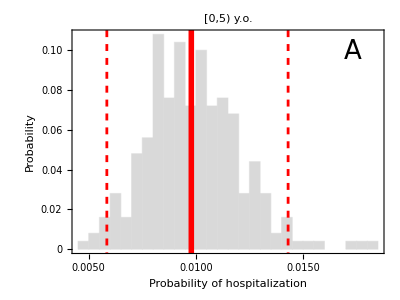
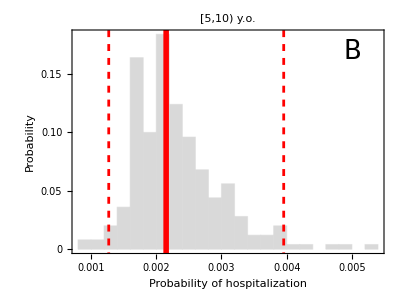
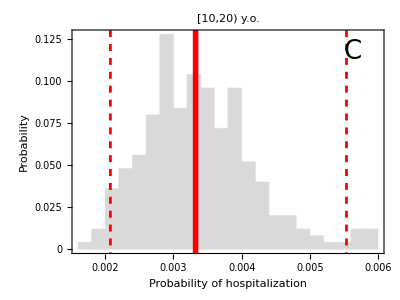
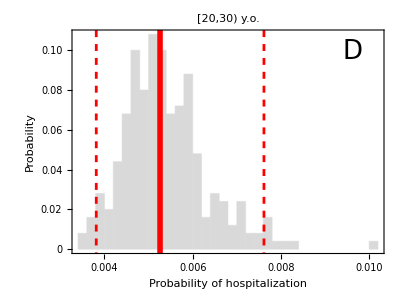
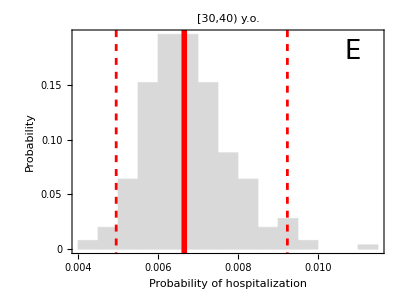
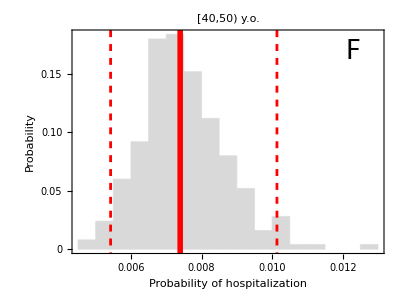
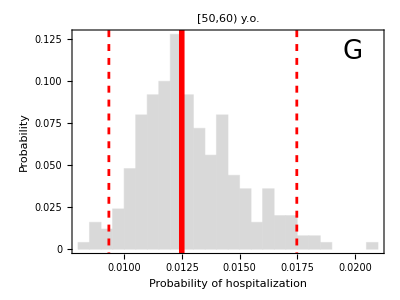
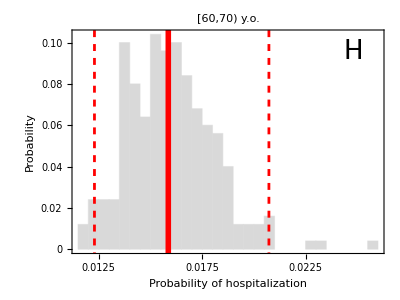

```mathematica
HistPlotLabel[vals_,xlab_,label_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->400,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray,PlotLabel->Style[Row[{label}],Black,17],PlotTheme->"Web"],Graphics[{Thickness[0.01],Red,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}]]

HistPlotLabelPanel[vals_,xlab_,label_,panel_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->400,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray,PlotLabel->Style[Row[{label}],Black,17],PlotTheme->"Web"],Graphics[{Thickness[0.01],Red,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}],Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]]

vals=Table[EstimatesData⟦All,14+i⟧,{i,1,10}];
xlab="Probability of hospitalization";

Table[{AgeLabel⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

FigNames={"A","B","C","D","E","F","G","H","I","J"};

Table[HistPlotLabelPanel[vals⟦i⟧,xlab,AgeLabel⟦i⟧,FigNames⟦i⟧],{i,1,Length[vals]}]
```

## Contact matrix Analytical form

```mathematica
ContactMatrix[t]:=((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+(1-1/(1+Exp[-K1 (t-x1)])) 1/(1+Exp[-K0 (t-x0)]) Subscript[ζ, 1] Subscript[d,{k,l}]+
1/(1+Exp[-K1 (t-x1)]) (u Subscript[c,{k,l}]+(1-u) Subscript[ζ, 1] Subscript[d,{k,l}])) (1-1/(1+Exp[-K2 (t-x2)]))+ 
1/(1+Exp[-K2 (t-x2)]) (Subscript[ζ, 2] Subscript[s,{k,l}]+Subscript[ζ, 3] (Subscript[c,{k,l}]-Subscript[s,{k,l}]));


ContactMatrixV[t]:=((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+(1-1/(1+Exp[-K1 (t-x1)])) 1/(1+Exp[-K0 (t-x0)]) Subscript[ζ, 1] Subscript[d,{k,l}]+1/(1+Exp[-K1 (t-x1)]) (u Subscript[c,{k,l}]+(1-u) Subscript[ζ, 1] Subscript[d,{k,l}])) (1-1/(1+Exp[-K2 (t-x2)]))+ 1/(1+Exp[-K2 (t-x2)]) (Subscript[ζ, 2] Subscript[s,{k,l}]+Subscript[ζ, 3] (Subscript[c,{k,l}]-Subscript[s,{k,l}]));
```

```mathematica
ContactMatrix[t]:=((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+(1-1/(1+Exp[-K1 (t-x1)])) 1/(1+Exp[-K0 (t-x0)]) Subscript[ζ, 1] Subscript[d,{k,l}]+
1/(1+Exp[-K1 (t-x1)]) (u Subscript[c,{k,l}]+(1-u) Subscript[ζ, 1] Subscript[d,{k,l}])) (1-1/(1+Exp[-K2 (t-x2)]))+ 
1/(1+Exp[-K2 (t-x2)]) (Subscript[ζ, 2] Subscript[s,{k,l}]+Subscript[ζ, 3] (Subscript[c,{k,l}]-Subscript[s,{k,l}]) (1-1/(1+Exp[-(t-260)])))+1/(1+Exp[-(t-260)])(0.3(*Subscript[ζ, 3]*) (Subscript[c,{k,l}]-Subscript[s,{k,l}]));


ContactMatrixV[t]:=((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+(1-1/(1+Exp[-K1 (t-x1)])) 1/(1+Exp[-K0 (t-x0)]) Subscript[ζ, 1] Subscript[d,{k,l}]+
1/(1+Exp[-K1 (t-x1)]) (u Subscript[c,{k,l}]+(1-u) Subscript[ζ, 1] Subscript[d,{k,l}])) (1-1/(1+Exp[-K2 (t-x2)]))+ 
1/(1+Exp[-K2 (t-x2)]) (Subscript[ζ, 2] Subscript[s,{k,l}]+Subscript[ζ, 3] (Subscript[c,{k,l}]-Subscript[s,{k,l}]) (1-1/(1+Exp[-(t-260)])))+1/(1+Exp[-(t-260)])(0.3(*Subscript[ζ, 3]*) (Subscript[c,{k,l}]-Subscript[s,{k,l}]));
```

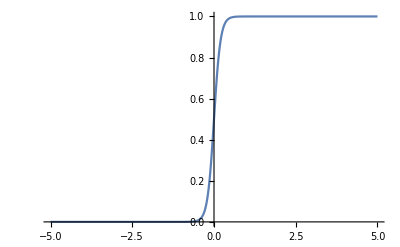

```mathematica
Plot[1/(1+Exp[-10t]),{t,-5,5}]
```

```mathematica
1616*36
```

58176

```mathematica
0.4*7+0.3*7+0.3*7
```

7.

## Model equations

```mathematica
TotNumVariables=11;
VarNumbers= Table[j, {j, 1, TotNumVariables}]
EqNumbers=Table[k,{k,1,NumAgeGroups TotNumVariables}]

Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t]-Subscript[r,k] Subscript[EE,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t]-Subscript[r,k] Subscript[R,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*+δ Subscript[H,k][t]*),
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]-Subscript[r,k] Subscript[H,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*-δ Subscript[H,k][t]*),
eq[Intervention_][6,k]:=Subscript[SV,k]'[t]==-(Subscript[λV,k][Intervention][t]Subscript[β,k]) Subscript[SV,k][t]+(1-Subscript[ω,k]) Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][7,k]:=Subscript[EEV,k]'[t]== Subscript[λV,k][Intervention][t]Subscript[β,k] Subscript[SV,k][t]-α Subscript[EEV,k][t]+Subscript[r,k] Subscript[EE,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][8,k]:=Subscript[IIV,k]'[t]== α Subscript[EEV,k][t]-(γ+Subscript[ν,k]) Subscript[IIV,k][t],
eq[Intervention_][9,k]:=Subscript[RV,k]'[t]== γ Subscript[IIV,k][t]+Subscript[r,k] Subscript[R,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*+δ Subscript[HV,k][t]*),
eq[Intervention_][10,k]:=Subscript[P,k]'[t]== Subscript[ω,k] Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][11,k]:=Subscript[HV,k]'[t]==Subscript[ν,k] Subscript[IIV,k][t]+Subscript[r,k] Subscript[H,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*-δ Subscript[HV,k][t]*)
(*eq[Intervention_][10,k]:=Subscript[VV,k]'[t]==Subscript[r,k]*)
},{k,AgeGroups}];

(*Table[Subscript[NN,k][t]=(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[R,k][t]+Subscript[H,k][t]+Subscript[SV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[RV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t]),{k,AgeGroups}];*)

NNtot=Sum[Subscript[NN,k],{k,AgeGroups}];

Table[Subscript[V,k][t]=Subscript[SV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[RV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],{k,AgeGroups}];

(* Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+1/(1+Exp[-KK (t-x0)]) ζ Subscript[d,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; *)

Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[ContactMatrix[t] (Subscript[II,l][t]+Subscript[IIV,l][t])/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; 

Table[Subscript[λV,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[ContactMatrixV[t] (Subscript[II,l][t]+Subscript[IIV,l][t])/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; 

Eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,TotNumVariables},{k,AgeGroups}]

TableForm[Eqs[Intervention]]

EqsList[Intervention_]:=Flatten[Flatten[Eqs[Intervention]]];

Total[EqsList[Intervention]⟦All,2⟧]//Simplify
```

{1,2,3,4,5,6,7,8,9,10,11}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110}

S_1'[t]==-(r_1 S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])-β_1 S_1[t] λ_1[Intervention][t] | S_2'[t]==-(r_2 S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])-β_2 S_2[t] λ_2[Intervention][t] | S_3'[t]==-(r_3 S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])-β_3 S_3[t] λ_3[Intervention][t] | S_4'[t]==-(r_4 S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])-β_4 S_4[t] λ_4[Intervention][t] | S_5'[t]==-(r_5 S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])-β_5 S_5[t] λ_5[Intervention][t] | S_6'[t]==-(r_6 S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])-β_6 S_6[t] λ_6[Intervention][t] | S_7'[t]==-(r_7 S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])-β_7 S_7[t] λ_7[Intervention][t] | S_8'[t]==-(r_8 S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])-β_8 S_8[t] λ_8[Intervention][t] | S_9'[t]==-(r_9 S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])-β_9 S_9[t] λ_9[Intervention][t] | S_10'[t]==-(r_10 S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])-β_10 S_10[t] λ_10[Intervention][t]
EE_1'[t]==-α EE_1[t]-(r_1 EE_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])+β_1 S_1[t] λ_1[Intervention][t] | EE_2'[t]==-α EE_2[t]-(r_2 EE_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])+β_2 S_2[t] λ_2[Intervention][t] | EE_3'[t]==-α EE_3[t]-(r_3 EE_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])+β_3 S_3[t] λ_3[Intervention][t] | EE_4'[t]==-α EE_4[t]-(r_4 EE_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])+β_4 S_4[t] λ_4[Intervention][t] | EE_5'[t]==-α EE_5[t]-(r_5 EE_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])+β_5 S_5[t] λ_5[Intervention][t] | EE_6'[t]==-α EE_6[t]-(r_6 EE_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])+β_6 S_6[t] λ_6[Intervention][t] | EE_7'[t]==-α EE_7[t]-(r_7 EE_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])+β_7 S_7[t] λ_7[Intervention][t] | EE_8'[t]==-α EE_8[t]-(r_8 EE_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])+β_8 S_8[t] λ_8[Intervention][t] | EE_9'[t]==-α EE_9[t]-(r_9 EE_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])+β_9 S_9[t] λ_9[Intervention][t] | EE_10'[t]==-α EE_10[t]-(r_10 EE_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])+β_10 S_10[t] λ_10[Intervention][t]
II_1'[t]==α EE_1[t]-(γ+ν_1) II_1[t] | II_2'[t]==α EE_2[t]-(γ+ν_2) II_2[t] | II_3'[t]==α EE_3[t]-(γ+ν_3) II_3[t] | II_4'[t]==α EE_4[t]-(γ+ν_4) II_4[t] | II_5'[t]==α EE_5[t]-(γ+ν_5) II_5[t] | II_6'[t]==α EE_6[t]-(γ+ν_6) II_6[t] | II_7'[t]==α EE_7[t]-(γ+ν_7) II_7[t] | II_8'[t]==α EE_8[t]-(γ+ν_8) II_8[t] | II_9'[t]==α EE_9[t]-(γ+ν_9) II_9[t] | II_10'[t]==α EE_10[t]-(γ+ν_10) II_10[t]
R_1'[t]==γ II_1[t]-(r_1 R_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | R_2'[t]==γ II_2[t]-(r_2 R_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | R_3'[t]==γ II_3[t]-(r_3 R_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | R_4'[t]==γ II_4[t]-(r_4 R_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | R_5'[t]==γ II_5[t]-(r_5 R_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | R_6'[t]==γ II_6[t]-(r_6 R_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | R_7'[t]==γ II_7[t]-(r_7 R_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | R_8'[t]==γ II_8[t]-(r_8 R_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | R_9'[t]==γ II_9[t]-(r_9 R_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | R_10'[t]==γ II_10[t]-(r_10 R_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
H_1'[t]==ν_1 II_1[t]-(r_1 H_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | H_2'[t]==ν_2 II_2[t]-(r_2 H_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | H_3'[t]==ν_3 II_3[t]-(r_3 H_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | H_4'[t]==ν_4 II_4[t]-(r_4 H_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | H_5'[t]==ν_5 II_5[t]-(r_5 H_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | H_6'[t]==ν_6 II_6[t]-(r_6 H_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | H_7'[t]==ν_7 II_7[t]-(r_7 H_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | H_8'[t]==ν_8 II_8[t]-(r_8 H_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | H_9'[t]==ν_9 II_9[t]-(r_9 H_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | H_10'[t]==ν_10 II_10[t]-(r_10 H_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
SV_1'[t]==(r_1 (1-ω_1) S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])-β_1 SV_1[t] λV_1[Intervention][t] | SV_2'[t]==(r_2 (1-ω_2) S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])-β_2 SV_2[t] λV_2[Intervention][t] | SV_3'[t]==(r_3 (1-ω_3) S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])-β_3 SV_3[t] λV_3[Intervention][t] | SV_4'[t]==(r_4 (1-ω_4) S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])-β_4 SV_4[t] λV_4[Intervention][t] | SV_5'[t]==(r_5 (1-ω_5) S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])-β_5 SV_5[t] λV_5[Intervention][t] | SV_6'[t]==(r_6 (1-ω_6) S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])-β_6 SV_6[t] λV_6[Intervention][t] | SV_7'[t]==(r_7 (1-ω_7) S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])-β_7 SV_7[t] λV_7[Intervention][t] | SV_8'[t]==(r_8 (1-ω_8) S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])-β_8 SV_8[t] λV_8[Intervention][t] | SV_9'[t]==(r_9 (1-ω_9) S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])-β_9 SV_9[t] λV_9[Intervention][t] | SV_10'[t]==(r_10 (1-ω_10) S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])-β_10 SV_10[t] λV_10[Intervention][t]
EEV_1'[t]==-α EEV_1[t]+(r_1 EE_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])+β_1 SV_1[t] λV_1[Intervention][t] | EEV_2'[t]==-α EEV_2[t]+(r_2 EE_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])+β_2 SV_2[t] λV_2[Intervention][t] | EEV_3'[t]==-α EEV_3[t]+(r_3 EE_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])+β_3 SV_3[t] λV_3[Intervention][t] | EEV_4'[t]==-α EEV_4[t]+(r_4 EE_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])+β_4 SV_4[t] λV_4[Intervention][t] | EEV_5'[t]==-α EEV_5[t]+(r_5 EE_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])+β_5 SV_5[t] λV_5[Intervention][t] | EEV_6'[t]==-α EEV_6[t]+(r_6 EE_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])+β_6 SV_6[t] λV_6[Intervention][t] | EEV_7'[t]==-α EEV_7[t]+(r_7 EE_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])+β_7 SV_7[t] λV_7[Intervention][t] | EEV_8'[t]==-α EEV_8[t]+(r_8 EE_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])+β_8 SV_8[t] λV_8[Intervention][t] | EEV_9'[t]==-α EEV_9[t]+(r_9 EE_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])+β_9 SV_9[t] λV_9[Intervention][t] | EEV_10'[t]==-α EEV_10[t]+(r_10 EE_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])+β_10 SV_10[t] λV_10[Intervention][t]
IIV_1'[t]==α EEV_1[t]-(γ+ν_1) IIV_1[t] | IIV_2'[t]==α EEV_2[t]-(γ+ν_2) IIV_2[t] | IIV_3'[t]==α EEV_3[t]-(γ+ν_3) IIV_3[t] | IIV_4'[t]==α EEV_4[t]-(γ+ν_4) IIV_4[t] | IIV_5'[t]==α EEV_5[t]-(γ+ν_5) IIV_5[t] | IIV_6'[t]==α EEV_6[t]-(γ+ν_6) IIV_6[t] | IIV_7'[t]==α EEV_7[t]-(γ+ν_7) IIV_7[t] | IIV_8'[t]==α EEV_8[t]-(γ+ν_8) IIV_8[t] | IIV_9'[t]==α EEV_9[t]-(γ+ν_9) IIV_9[t] | IIV_10'[t]==α EEV_10[t]-(γ+ν_10) IIV_10[t]
RV_1'[t]==γ IIV_1[t]+(r_1 R_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | RV_2'[t]==γ IIV_2[t]+(r_2 R_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | RV_3'[t]==γ IIV_3[t]+(r_3 R_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | RV_4'[t]==γ IIV_4[t]+(r_4 R_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | RV_5'[t]==γ IIV_5[t]+(r_5 R_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | RV_6'[t]==γ IIV_6[t]+(r_6 R_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | RV_7'[t]==γ IIV_7[t]+(r_7 R_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | RV_8'[t]==γ IIV_8[t]+(r_8 R_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | RV_9'[t]==γ IIV_9[t]+(r_9 R_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | RV_10'[t]==γ IIV_10[t]+(r_10 R_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
P_1'[t]==(r_1 ω_1 S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | P_2'[t]==(r_2 ω_2 S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | P_3'[t]==(r_3 ω_3 S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | P_4'[t]==(r_4 ω_4 S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | P_5'[t]==(r_5 ω_5 S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | P_6'[t]==(r_6 ω_6 S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | P_7'[t]==(r_7 ω_7 S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | P_8'[t]==(r_8 ω_8 S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | P_9'[t]==(r_9 ω_9 S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | P_10'[t]==(r_10 ω_10 S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
HV_1'[t]==ν_1 IIV_1[t]+(r_1 H_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | HV_2'[t]==ν_2 IIV_2[t]+(r_2 H_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | HV_3'[t]==ν_3 IIV_3[t]+(r_3 H_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | HV_4'[t]==ν_4 IIV_4[t]+(r_4 H_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | HV_5'[t]==ν_5 IIV_5[t]+(r_5 H_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | HV_6'[t]==ν_6 IIV_6[t]+(r_6 H_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | HV_7'[t]==ν_7 IIV_7[t]+(r_7 H_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | HV_8'[t]==ν_8 IIV_8[t]+(r_8 H_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | HV_9'[t]==ν_9 IIV_9[t]+(r_9 H_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | HV_10'[t]==ν_10 IIV_10[t]+(r_10 H_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])

0

## Model variables

```mathematica
varsS=Table[Subscript[S,k][t],{k,AgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,AgeGroups}];
varsII=Table[Subscript[II,k][t],{k,AgeGroups}];
varsR=Table[Subscript[R,k][t],{k,AgeGroups}];
varsH=Table[Subscript[H,k][t],{k,AgeGroups}];

varsSV=Table[Subscript[SV,k][t],{k,AgeGroups}];
varsEEV=Table[Subscript[EEV,k][t],{k,AgeGroups}];
varsIIV=Table[Subscript[IIV,k][t],{k,AgeGroups}];
varsRV=Table[Subscript[RV,k][t],{k,AgeGroups}];
varsP=Table[Subscript[P,k][t],{k,AgeGroups}];
varsHV=Table[Subscript[HV,k][t],{k,AgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totSV=Total[Total[varsSV]];
totEEV=Total[Total[varsEEV]];
totIIV=Total[Total[varsIIV]];
totRV=Total[Total[varsRV]];
totP=Total[Total[varsP]];
totHV=Total[Total[varsHV]];

totVars={totS,totEE,totII,totR,totH,totSV,totEEV,totIIV,totRV,totP,totHV};
totVarsYlab={"S(t)","E(t)","I(t)","R(t)","H(t)","S^V(t)","E^V(t)","I^V(t)","R^V(t)","P(t)","H^V(t)"};

ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t],Subscript[SV,k][t],Subscript[EEV,k][t],Subscript[IIV,k][t],Subscript[RV,k][t],Subscript[P,k][t],Subscript[HV,k][t],Subscript[V,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)","(S^V)_k(t)","(E^V)_k(t)","(I^V)_k(t)","(R^V)_k(t)","P_k(t)","(H^V)_k(t)","V_k(t)"};

Vars=Join[varsS,varsEE,varsII,varsR,varsH,varsSV,varsEEV,varsIIV,varsRV,varsP,varsHV];
VarsList=Flatten[Vars];

hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]+Subscript[IIV,k][t]),{k,AgeGroups}];

InfIncidenceVars=Table[α (Subscript[EE,k][t]+Subscript[EEV,k][t]),{k,AgeGroups}];

VacPropVars=Table[Subscript[V,k][t]/Subscript[NN,k],{k,AgeGroups}];
```

## Initial conditions Solving equations with and without vaccination Vaccination stops when all individuals in a given age group get vaccinated Other conditions are possible MAP parameter sample

```mathematica
Subscript[t, start]=t0;
Subscript[t, end]=tendvac;

ICs=Table[ic[j,k],{j,VarNumbers},{k,AgeGroups}];
ICsList=Flatten[Flatten[ICs]];
Dimensions[ICsList];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[6,k]=0==Subscript[SV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[7,k]=0==Subscript[EEV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[8,k]=0==Subscript[IIV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[9,k]=0==Subscript[RV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[10,k]=0==Subscript[P,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[11,k]=0==Subscript[HV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];

intList={"Estimation"};

solution[Intervention_,pars_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.pars,VarsList,{t,Subscript[t, start],Subscript[t, end]}, Method->"StiffnessSwitching"];

Table[sol[it]=solution[intList⟦it⟧,ParametersMAPNoVaccination],{it,1,Length[intList]}];
Table[solVac[it]=solution[intList⟦it⟧,ParametersMAPVaccination],{it,1,Length[intList]}];

AspRat=0.75;
ImSize=250;

PlottotVars[sol_]:=Grid[Table[Table[Plot[Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.sol[it]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{Thick,Darker[Blue]},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]];

PlotageVars[sol_]:=Grid[Table[Table[Plot[
Evaluate[Table[(ageVars⟦i⟧/Subscript[NN,k]/.Demography)/.sol[it],{k,AgeGroups}]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->"DarkRainbow",AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{ageVarsYlab⟦i⟧,None},{"Days",None}},PlotLegends->Placed[AgeLabelShort,Right]],{i,1,Length[ageVars]}],{it,1,Length[intList]}]];

PlottotVarsComparison=Grid[Table[Table[Plot[{Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.sol[it]],Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.solVac[it]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Red]}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]];
```

## Prevalence of individuals in different classes Prevalence of individuals in different classes per age group

Solutions without vaccination

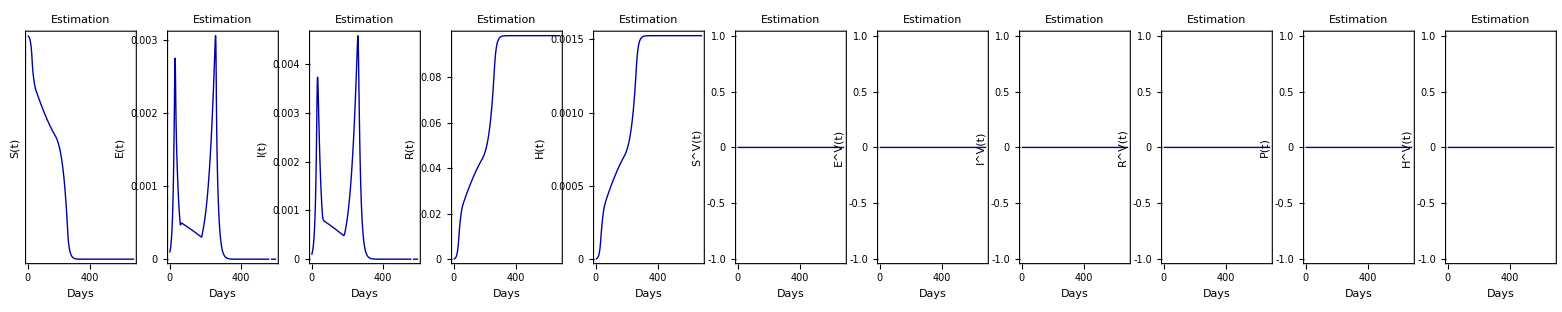

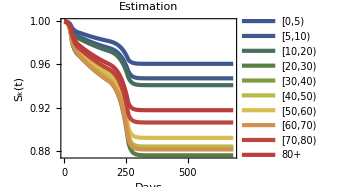
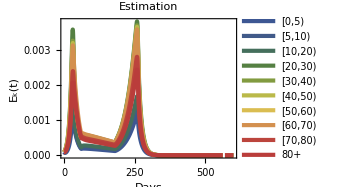
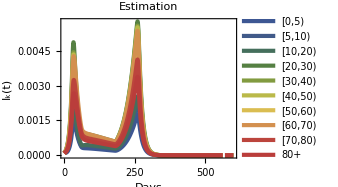
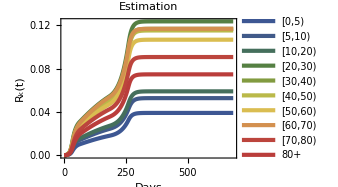
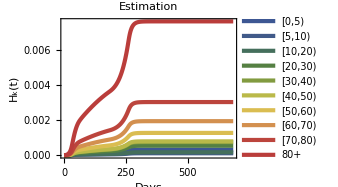
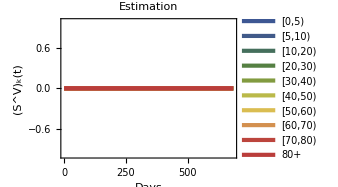
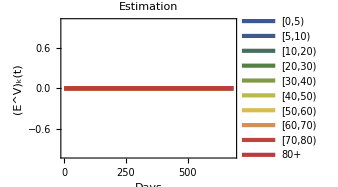
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Solutions with vaccination

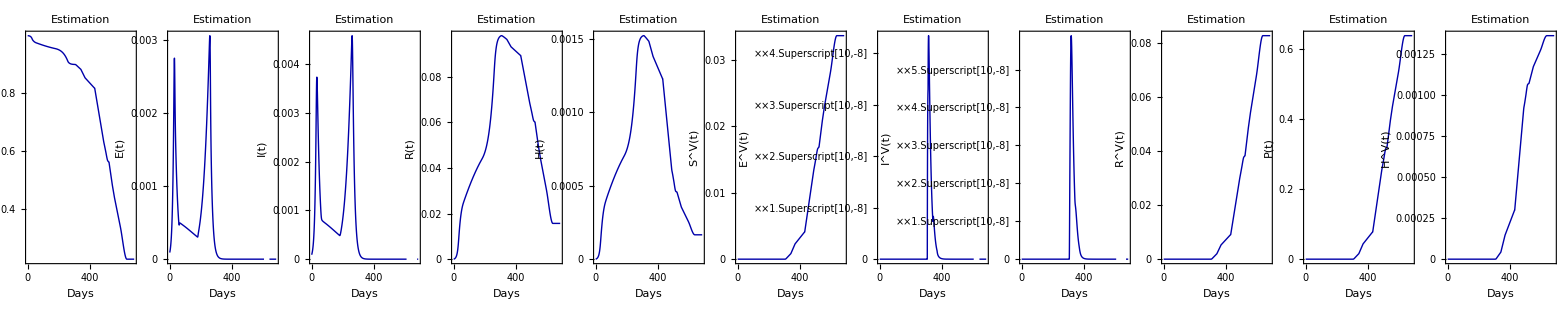

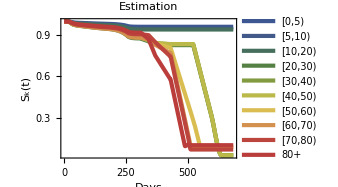
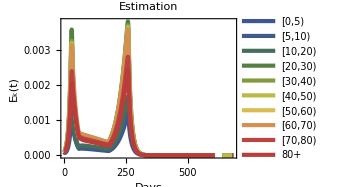
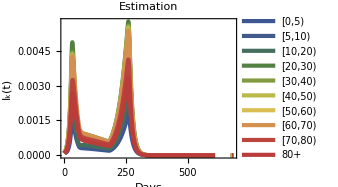
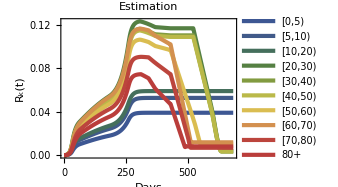
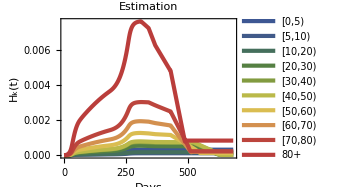
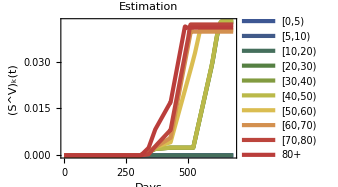
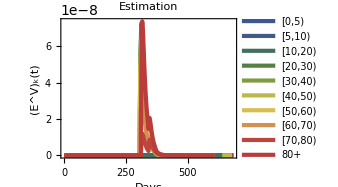
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Comparison solutions without and with vaccination

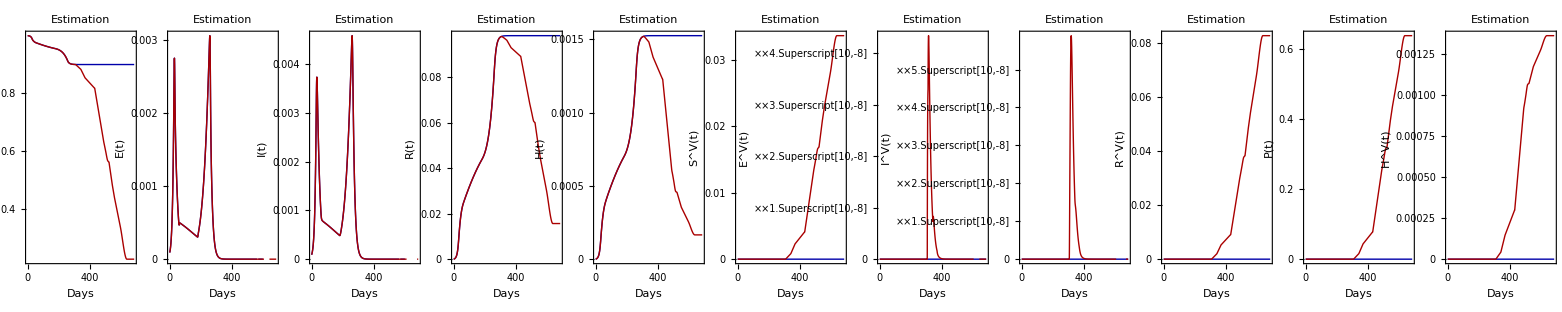

Solutions without vaccination

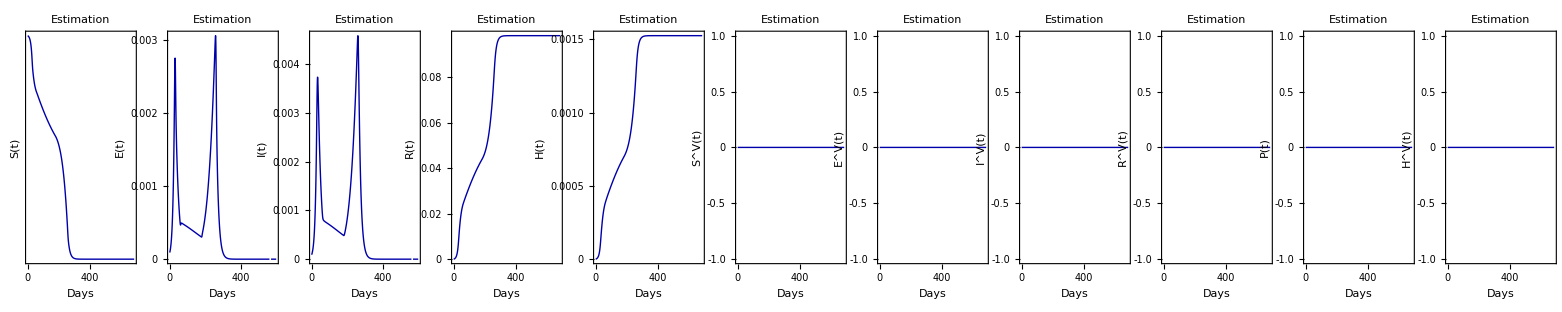

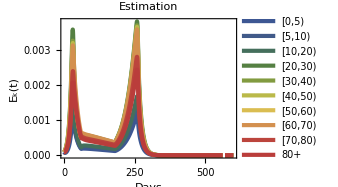
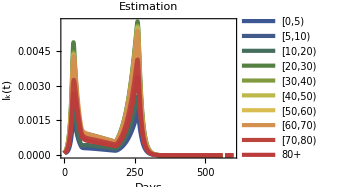
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Solutions with vaccination

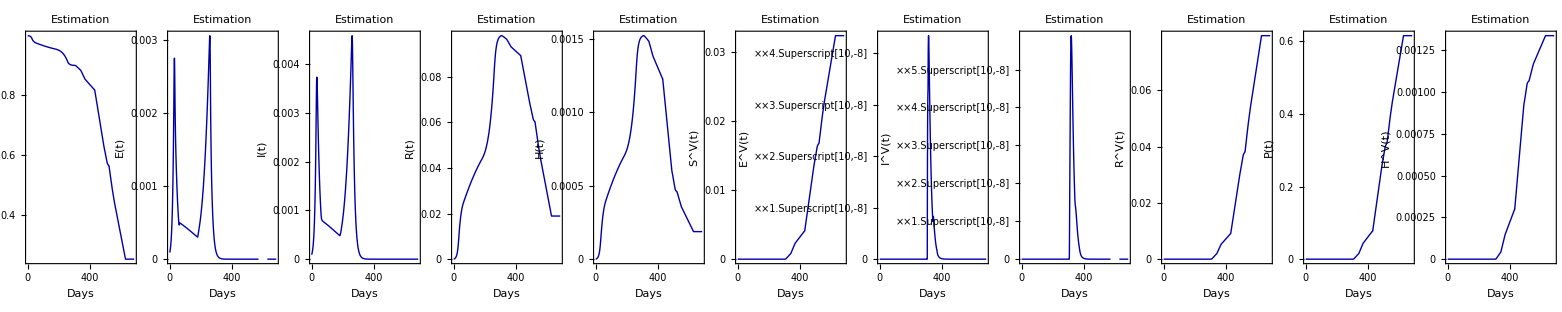

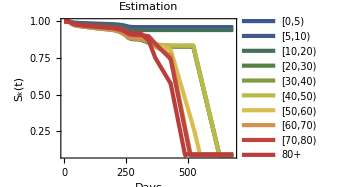
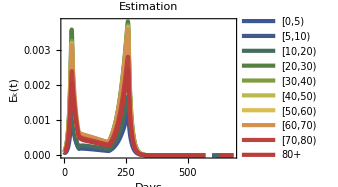
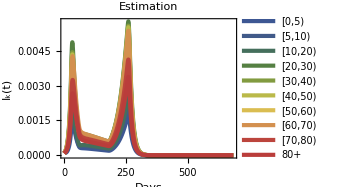
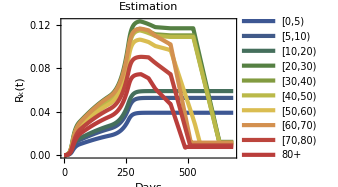
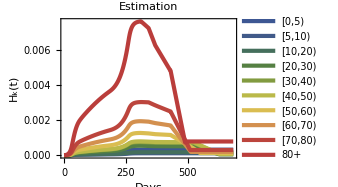
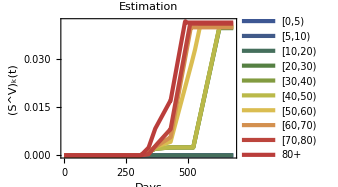
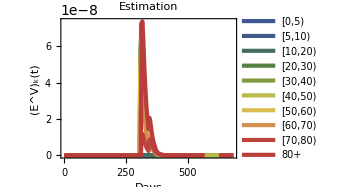
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Comparison solutions without and with vaccination

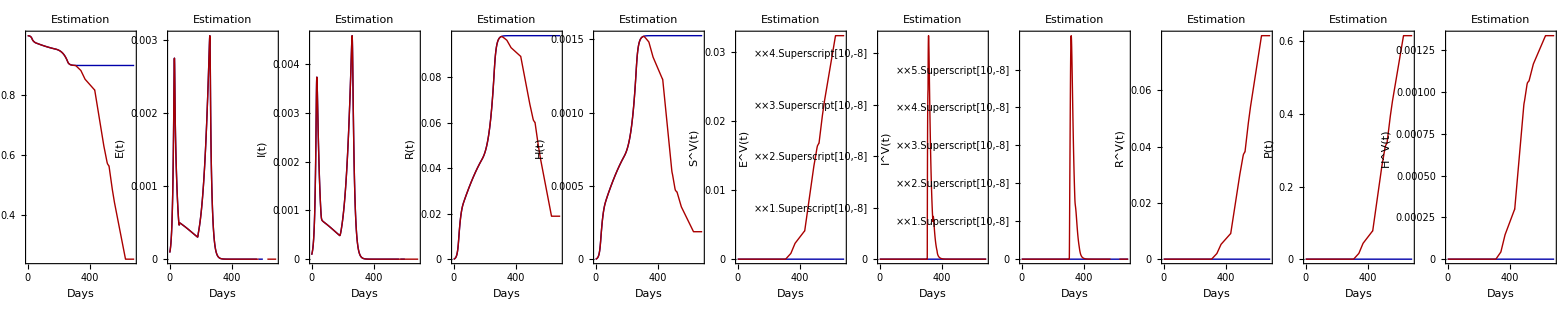

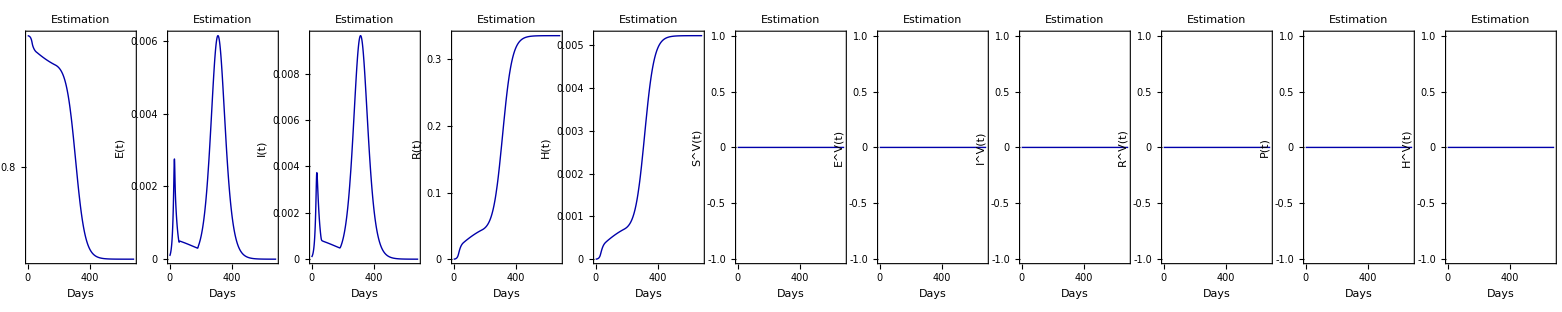

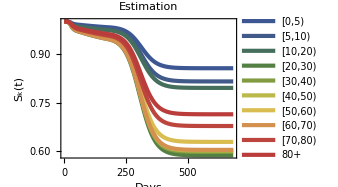
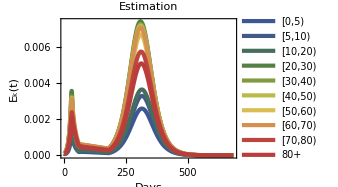
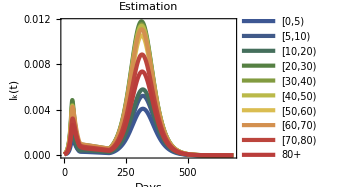
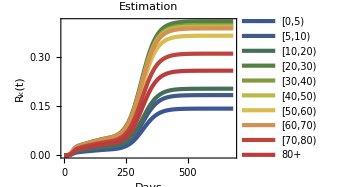
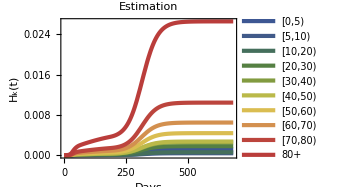
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Solutions with vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Comparison solutions without and with vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Print[Style["Solutions without vaccination",18,Blue,"Text"]]
PlottotVars[sol]
PlotageVars[sol]

Print[Style["Solutions with vaccination",18,Blue,"Text"]]
PlottotVars[solVac]
PlotageVars[solVac]

Print[Style["Comparison solutions without and with vaccination",18,Blue,"Text"]]
PlottotVarsComparison
```

```mathematica
Memory
```

Memory Used:125.683 MB

# Execution

## Choose times and samples

```mathematica
Subscript[t, step]=1;
Subscript[t, end]=tendvac;

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=20;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];

HospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[ListSamples⟦sample⟧]]],0],{k,AgeGroups},{sample,1,Length[ListSamples]},{t,1,Dimensions[var]⟦3⟧}];

ExportData[var_,filename_]:=Table[Export[StringJoin["MathematicaFiles//",filename,ToString[k],".txt"],var⟦k⟧,"Table"],{k,AgeGroups}];
```

## Solutions with credible intervals

## No vaccination

```mathematica
(**********************************************************)


ParametersAll=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

solAll=Table[NDSolve[Join[EqsList["Estimation"],ICsList]/.ParametersAll⟦i⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]} ,Method->"StiffnessSwitching"],{i,1,Length[ListSamples]}];

Trajectories[var_]:=Table[Table[Table[Evaluate[(var⟦k⟧/.ParametersAll⟦i⟧)/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

HospIncidence1=Trajectories[hospVars];
ExportData[HospIncidence1,"HospIncidence"];

InfIncidence1=Trajectories[InfIncidenceVars];
ExportData[InfIncidence1,"InfIncidence"];

HospIncidenceSimulated1=HospSimulated[HospIncidence1];
ExportData[HospIncidenceSimulated1,"HospIncidenceSimulated"];

Memory
```

Memory Used:160.654 MB

## Solutions with credible intervals

## Vaccination (high vaccine efficacy)

```mathematica
Clear[ParametersAll,solAll,Trajectories]

ParametersAll=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];

solAll=Table[NDSolve[Join[EqsList["Estimation"],ICsList]/.ParametersAll⟦i⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]} ,Method->"StiffnessSwitching"],{i,1,Length[ListSamples]}];

Trajectories[var_]:=Table[Table[Table[Evaluate[(var⟦k⟧/.ParametersAll⟦i⟧)/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

(*HospIncidenceVac=Trajectories[hospVars];
ExportData[HospIncidenceVac,"HospIncidenceVac"];

InfIncidenceVac=Trajectories[InfIncidenceVars];
ExportData[InfIncidenceVac,"InfIncidenceVac"];

HospIncidenceSimulatedVac=HospSimulated[HospIncidenceVac];
ExportData[HospIncidenceSimulatedVac,"HospIncidenceSimulatedVac"];*)

VaccinatedProportion=Trajectories[VacPropVars];
ExportData[VaccinatedProportion,"VaccinatedProportion"];

Memory
```

Memory Used:491.858 MB

# Plotting

## Preliminaries

```mathematica
HospIncidence=Table[Import[StringJoin["MathematicaFiles//HospIncidence",ToString[k],".txt"],"Table"],{k,AgeGroups}];
InfIncidence=Table[Import[StringJoin["MathematicaFiles//InfIncidence",ToString[k],".txt"],"Table"],{k,AgeGroups}];
HospIncidenceSimulated=Table[Import[StringJoin["MathematicaFiles//HospIncidenceSimulated",ToString[k],".txt"],"Table"],{k,AgeGroups}];

HospIncidenceVac=Table[Import[StringJoin["MathematicaFiles//HospIncidenceVac",ToString[k],".txt"],"Table"],{k,AgeGroups}];
InfIncidenceVac=Table[Import[StringJoin["MathematicaFiles//InfIncidenceVac",ToString[k],".txt"],"Table"],{k,AgeGroups}];
HospIncidenceSimulatedVac=Table[Import[StringJoin["MathematicaFiles//HospIncidenceSimulatedVac",ToString[k],".txt"],"Table"],{k,AgeGroups}];
VaccinatedProportion=Table[Import[StringJoin["MathematicaFiles//VaccinatedProportion",ToString[k],".txt"],"Table"],{k,AgeGroups}];
```

## Plot vaccination coverage

```mathematica
Print[Style["Vaccinated proportion (%) in each age group",24,Blue,"Text"]];

(*Table[Show[
ListLinePlot[VaccinatedProportion⟦k,1⟧,AspectRatio->AspRat,ImageSize->350,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,1}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Vaccinated proportion (%)",None},{"Days",None}},Filling->None(*{{3->{2}},{5-> {4}}}*),PlotStyle->{Blue,Thick},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17],Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDays⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDays]}]]],Graphics[Text[StyleForm[FigNames⟦k⟧,FontSize->26],Scaled[{0.9,0.9}]]]
],{k,AgeGroups}]*)

AspRat=0.75; ImSize=350;

(*tickValues=DateRange[{2020,3},{2021,12},{4,"Month"}]⟦All,{1,2}⟧;
ticks=tickValues;*)

tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

BarChartLegends=Style[#,Black]&/@{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

ChartStyleColors=Join[{Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]](*ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0]*)},ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;7⟧]];

LineWidthsAll=Table[Thickness[0.005],{k,AgeGroups}];

SFig5=Show[
DateListPlot[Table[VaccinatedProportion⟦k,1⟧ 100,{k,AgeGroups}],"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-1,100}},AspectRatio->AspRat,ImageSize->500,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{0,0},FrameLabel-> {{"Vaccination coverage (%)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotLegends->Placed[BarChartLegends,Scaled[{{0.25, 0.450}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->ChartStyleColors(*Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[Text[StyleForm["equal coverage in [20,50) y.o.",FontSize->12],Scaled[{0.2,0.95}]]],Graphics[Text[StyleForm["zero coverage in [0,20) y.o.",FontSize->12],Scaled[{0.185,0.9}]]]]

Table[Export[StringJoin["Figures//SFig5",format⟦i⟧],SFig5],{i,1,Length[format]}];

(*Labeled[Style[Text["curves coincide"],FontFamily->"Arial",FontSize->12],Alignment->{Top,Center}(*Close Labeled*)]*)

fig2A=Show[
DateListPlot[Table[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}]/100000,"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-0.1,All}},AspectRatio->AspRat,ImageSize->500,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{0,0},FrameLabel-> {{"Vaccinated persons (x 100000)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotLegends->Placed[BarChartLegends,Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->ChartStyleColors(*Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,Automatic}}],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.07,0.9}]]]];

(*Table[Export[StringJoin["Figures//Fig2A",format⟦i⟧],fig2A],{i,1,Length[format]}];*)

fig2B=Show[
DateListPlot[Sum[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}] 100/Total[DemographyData10],"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-0.75,100}},AspectRatio->AspRat,ImageSize->500,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{0,0},FrameLabel-> {{"Vaccination coverage (%)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotStyle->{Black}(*,PlotLegends->Placed[Style[#,Black]&/@{"[20,80+) y.o."},Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,Automatic}}],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.07,0.9}]]]];


fig2=Grid[{{fig2A,fig2B}}]

Table[Export[StringJoin["Figures//Fig2",format⟦i⟧],fig2],{i,1,Length[format]}];
```

Vaccinated proportion (%) in each age group

-Graphics-

-Graphics- | -Graphics-

## Plotting functions

```mathematica
ImSize=350;
AspRat=0.75;

ticks=DateRange[{2020,3},{2021,12},{4,"Month"}]⟦All,{1,2}⟧;

UniqueStartVaccinationDates=DeleteDuplicates[Join[StartAndEndVaccinationDates⟦1⟧⟦All,1⟧,StartAndEndVaccinationDates⟦2⟧⟦All,1⟧,{StartAndEndVaccinationDates⟦3⟧⟦1⟧}]];

VaccinationLines:=Table[DateListPlot[{{UniqueStartVaccinationDates⟦i⟧,0},{UniqueStartVaccinationDates⟦i⟧,10000}},PlotStyle->{Dashed,Gray},DateTicksFormat->{"MonthShort","/","YearShort"}],{i,1,Length[UniqueStartVaccinationDates]}];

DatePlot[AgeGroup_]:=DateListPlot[HospitalisationsData⟦All,AgeGroup⟧,"February 26, 2020",PlotMarkers->{Automatic,Tiny},PlotTheme->"Web",Joined-> False,DateTicksFormat->{"MonthShort","/","YearShort"}]

PlotDataAndModel[Var_,VarSimulated_,tendplot_,onlydata_]:=Grid[{Reverse[Table[Show[
DateListPlot[{Median[Var⟦k⟧],Quantile[Var⟦k⟧,0.025],Quantile[Var⟦k⟧,0.975],Quantile[VarSimulated⟦k⟧,0.025],Quantile[VarSimulated⟦k⟧,0.975]},"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[VarSimulated⟦k⟧,0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"Hospitalizations",None},{None,None}},Filling->{{3->{2}},{5->{4}}},PlotStyle->{{Black,Thick},Darker[Gray],Darker[Gray],Lighter[Gray],Lighter[Gray]},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17]],DatePlot[k],VaccinationLines,PanelLetter[k]],{k,AgeGroups}]]}]

ComparisonDataModelVacAndNoVac[Var1_,Var2_,tendplot_]:=Grid[{Reverse[Table[Show[
DateListPlot[{Median[Var1⟦k⟧],Quantile[Var1⟦k⟧,0.025],Quantile[Var1⟦k⟧,0.975],Median[Var2⟦k⟧],Quantile[Var2⟦k⟧,0.025],Quantile[Var2⟦k⟧,0.975]},"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},All},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"Hospitalizations",None},{None,None}},Filling->{{3->{2}},{6->{5}}},PlotStyle->{{Black,Thick},{Gray,Thin},{Gray,Thin},{Yellow,Thick},{Yellow,Thin},{Yellow,Thin}},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17]],DatePlot[k],VaccinationLines,PanelLetter[k]],{k,AgeGroups}]]}]

ComparisonModelVacAndNoVac[Var1_,Var2_,tendplot_]:=Grid[{Reverse[Table[Show[
DateListPlot[{Median[Var1⟦k⟧],Quantile[Var1⟦k⟧,0.025],Quantile[Var1⟦k⟧,0.975],Median[Var2⟦k⟧],Quantile[Var2⟦k⟧,0.025],Quantile[Var2⟦k⟧,0.975]},"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},All},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"New cases",None},{None,None}},Filling->{{3->{2}},{6->{5}}},PlotStyle->{{Black,Thick},{Gray,Thin},{Gray,Thin},{Yellow,Thick},{Yellow,Thin},{Yellow,Thin}},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17]],VaccinationLines,PanelLetter[k]],{k,AgeGroups}]]}]

PlotDataAndIndividualTrajectories[Var_,tendplot_,onlydata_]:=Grid[{Reverse[Table[Show[
DateListPlot[Table[Var⟦k⟧⟦n⟧,{n,Length[Var⟦k⟧]}],"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[Var⟦k⟧,0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"Hospitalizations",None},{None,None}},Filling->None,PlotStyle->{Gray},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17]],DatePlot[k],VaccinationLines,PanelLetter[k]],{k,AgeGroups}]]}]

PlotIndividualTrajectories[Var_,tendplot_,onlydata_]:=Grid[{Reverse[Table[Show[
DateListPlot[Table[Var⟦k⟧⟦n⟧,{n,Length[Var⟦k⟧]}],"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[Var⟦k⟧,0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"New cases",None},{None,None}},Filling->None,PlotStyle->{Gray},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17]],VaccinationLines,PanelLetter[k]],{k,AgeGroups}]]}]
```

## Figures

```mathematica
Memory

Print[Style["New hospitalizations (per day) in each age group",24,Blue,"Text"]];
Print[Style["Median trajectories and credible intervals",24,Blue,"Text"]];
PlotDataAndModel[HospIncidence,HospIncidenceSimulated,"November 6, 2020",True]

Memory

Print[Style["Model with vaccination",18,Red,"Text"]]
PlotDataAndModel[HospIncidenceVac,HospIncidenceSimulatedVac,"August 11, 2021",False]

Memory

Print[Style["Comparison of the model with and without vaccination",18,Red,"Text"]]
ComparisonDataModelVacAndNoVac[HospIncidence,HospIncidenceVac,"August 11, 2021"]

Memory

Print[Style["Individual trajectories",24,Blue,"Text"]];
Print[Style["Model with vaccination",18,Red,"Text"]]
PlotDataAndIndividualTrajectories[HospIncidenceVac,"August 11, 2021",False]

Memory

Print[Style["Infection incidence (new cases per day) in each age group",24,Blue,"Text"]];
Print[Style["Individual trajectories",24,Blue,"Text"]];
Print[Style["Model with vaccination",18,Red,"Text"]]
PlotIndividualTrajectories[InfIncidenceVac,"August 11, 2021",False]

Memory

Print[Style["Comparison of the model with and without vaccination",18,Red,"Text"]]
ComparisonModelVacAndNoVac[InfIncidence,InfIncidenceVac,"August 11, 2021"]

Memory
```

Memory Used:157.005 MB

New hospitalizations (per day) in each age group

Median trajectories and credible intervals

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Memory Used:169.678 MB

Model with vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Memory Used:182.318 MB

Comparison of the model with and without vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Memory Used:197.145 MB

Individual trajectories

Model with vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Memory Used:243.34 MB

Infection incidence (new cases per day) in each age group

Individual trajectories

Model with vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Memory Used:288.089 MB

Comparison of the model with and without vaccination

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Memory Used:301.6 MB

```mathematica
ImSize=350;
AspRat=0.75;

ticks=DateRange[{2020,3},{2021,12},{4,"Month"}]⟦All,{1,2}⟧;

UniqueStartVaccinationDates=DeleteDuplicates[Join[StartAndEndVaccinationDates⟦1⟧⟦All,1⟧,StartAndEndVaccinationDates⟦2⟧⟦All,1⟧,{StartAndEndVaccinationDates⟦3⟧⟦1⟧}]];

VaccinationLines:=Table[DateListPlot[{{UniqueStartVaccinationDates⟦i⟧,0},{UniqueStartVaccinationDates⟦i⟧,10000}},PlotStyle->{Dashed,Gray},DateTicksFormat->{"MonthShort","/","YearShort"}],{i,1,Length[UniqueStartVaccinationDates]}];

DatePlotAll:=DateListPlot[Total[Transpose[HospitalisationsData]],"February 26, 2020",PlotMarkers->{Automatic,Tiny},PlotTheme->"Web",Joined-> False,DateTicksFormat->{"MonthShort","/","YearShort"}]

PlotTotalDataAndModel[Var_,VarSimulated_,tendplot_,onlydata_,plotlabel_]:=Show[DateListPlot[{Median[Total[Var]],Quantile[Total[Var],0.025],Quantile[Total[Var],0.975],Quantile[Total[VarSimulated],0.025],Quantile[Total[VarSimulated],0.975]},"February 25, 2020",FrameTicks->{{Automatic,None},{ticks,None}},DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[Total[VarSimulated],0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"New hospitalizations (1/day)",None},{None,None}},Filling->{{3->{2}},{5->{4}}},PlotStyle->{{Black,Thick},Darker[Gray],Darker[Gray],Lighter[Gray],Lighter[Gray]},PlotLabel->Style[Row[{plotlabel}],Black,17]],DatePlotAll,VaccinationLines(*,PanelLetter[k]*)]

(*PlotTotalDataAndModel[HospIncidence,HospIncidenceSimulated,"November 6, 2020",True,"Model fit"]*)
PlotTotalDataAndModel[HospIncidence1,HospIncidenceSimulated1,"November 6, 2020",True,"Model fit"]


(*PlotTotalDataAndModel[HospIncidence,HospIncidenceSimulated,"August 11, 2021",False,"No vaccination"]*)
PlotTotalDataAndModel[HospIncidence1,HospIncidenceSimulated1,"August 11, 2021",False,"No vaccination"]
(*PlotTotalDataAndModel[HospIncidenceVac,HospIncidenceSimulatedVac,"August 11, 2021",False,"Vaccination"]*)
```

-Graphics-

-Graphics-

## Calculating R_e

## Takes LONG! Needs improvement!

```mathematica
Subscript[t, start]=0;
Subscript[t, endData]=Dimensions[HospitalisationsData]⟦1⟧+2;
Subscript[t, step]=3;

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=100;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

ParametersNoVaccinationAll=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

solutionCrI[Intervention_,sample_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.ParametersNoVaccinationAll⟦sample⟧,VarsList,{t,Subscript[t, start],Subscript[t, endData]} ];
solutionCrIAll=Table[solutionCrI["Estimation",i],{i,1,Length[ListSamples]}];

VarSampleAtTimet[var_,sample_,tRe_]:=(Evaluate[var/.First@solutionCrIAll⟦sample⟧])/.t-> tRe;

(* DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->Subscript[NN,k]-VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->0,Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->0,Subscript[P,k][t]->0},{k,AgeGroups}]]; *)

DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->VarSampleAtTimet[Subscript[R,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[H,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->VarSampleAtTimet[Subscript[SV,k][t],sample,tRe],Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->VarSampleAtTimet[Subscript[RV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],sample,tRe],Subscript[P,k][t]->0,Subscript[HV,k][t]->0},{k,AgeGroups}]];

EqNumbersRe=Join[EqNumbers⟦NumAgeGroups+1;;3 NumAgeGroups⟧,EqNumbers⟦6 NumAgeGroups+1;;8 NumAgeGroups⟧];

JacobAnalyt=Table[ D[EqsList["Estimation"]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersRe} ,{p,EqNumbersRe}];
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalyt⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersRe]} ,{p,1,Length[EqNumbersRe]}];
TransitionMatrix=JacobAnalyt-TransmissionMatrix;

TransmissionMatrixSampleAtTimet[sample_,tRe_]:=((TransmissionMatrix/.DiseaseState[sample,tRe])/.ParametersNoVaccinationAll⟦sample⟧)/.t->tRe ;

TransitionMatrixSampleAtTimet[sample_,tRe_]:=((TransitionMatrix/.DiseaseState[sample,tRe])/.ParametersNoVaccinationAll⟦sample⟧)/.t->tRe;

ReSampleAtTimet[sample_,tRe_]:=Re[Eigenvalues[-TransmissionMatrixSampleAtTimet[sample,tRe].Inverse[TransitionMatrixSampleAtTimet[sample,tRe]]]⟦1⟧];

TrajectoriesRe=Table[Transpose[{Table[t,{t,Subscript[t, start],Subscript[t, endData],Subscript[t, step]}],Table[ReSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, endData],Subscript[t, step]}]}],{i,1,Length[ListSamples]}];

DateListPlot[{Median[TrajectoriesRe]⟦All,2⟧,Quantile[TrajectoriesRe,0.025]⟦All,2⟧,Quantile[TrajectoriesRe,0.975]⟦All,2⟧},{{2020,02,26},Automatic,{0,0,Subscript[t, step]}},DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->0.75,ImageSize->450,PlotRangePadding->None,PlotRange->{All,{0,Automatic}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"R_e",None},{None,None}},Filling->{3->{2}},PlotStyle->{Black,Darker[Gray],Darker[Gray]},PlotLabel->Style[Row[{"R_e trajectories"}],Black,17],Prolog->{Directive[{Dashed,Thick,Red}],InfiniteLine[{{0,1},{2,1}}]}]

DateListPlot[Table[TrajectoriesRe⟦n⟧⟦All,2⟧,{n,Length[ListSamples]}],{{2020,02,26},Automatic,{0,0,Subscript[t, step]}},DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->0.75,ImageSize->450,PlotRangePadding->None,PlotRange->{All,{0,Automatic}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"R_e",None},{None,None}},PlotLabel->Style[Row[{"Individual R_e trajectories"}],Black,17],Prolog->{Directive[{Dashed,Thick,Red}],InfiniteLine[{{0,1},{2,1}}]}]

Table[DateListPlot[TrajectoriesRe⟦n⟧⟦All,2⟧,{{2020,02,26},Automatic,{0,0,Subscript[t, step]}},DateTicksFormat->{"MonthShort","/","YearShort"},AspectRatio->0.75,ImageSize->250,PlotRangePadding->None,PlotRange->{All,{0,Automatic}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"R_e",None},{None,None}},PlotLabel->Style[Row[{"Individual R_e trajectories ",n}],Black,17],Prolog->{Directive[{Dashed,Thick,Red}],InfiniteLine[{{0,1},{2,1}}]}],{n,Length[ListSamples]}]
```

-Graphics-

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=500(*Dimensions[HospitalisationsData]⟦1⟧+2*);
Subscript[t, step]=7;

nSamples=81(*Dimensions[EstimatesData]⟦1⟧*);
stepSamples=20;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

ParametersNoVaccinationAll=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

ParametersVaccination[sample_]:=Join[Parameters[sample],Rates,VacEffHigh];
ParametersVaccinationAll=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];

solutionCrI[Intervention_,sample_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.ParametersVaccinationAll⟦sample⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]},Method->"StiffnessSwitching"];
solutionCrIAll=Table[solutionCrI["Estimation",i],{i,1,Length[ListSamples]}];

VarSampleAtTimet[var_,sample_,tRe_]:=(Evaluate[var/.First@solutionCrIAll⟦sample⟧])/.t-> tRe;

(* DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->Subscript[NN,k]-VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->0,Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->0,Subscript[P,k][t]->0},{k,AgeGroups}]]; *)

DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->VarSampleAtTimet[Subscript[R,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[H,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->VarSampleAtTimet[Subscript[SV,k][t],sample,tRe],Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->VarSampleAtTimet[Subscript[RV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],sample,tRe],Subscript[P,k][t]->0,Subscript[HV,k][t]->0},{k,AgeGroups}]];

EqNumbersRe=Join[EqNumbers⟦NumAgeGroups+1;;3 NumAgeGroups⟧,EqNumbers⟦6 NumAgeGroups+1;;8 NumAgeGroups⟧];

JacobAnalyt=Table[ D[EqsList["Estimation"]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersRe} ,{p,EqNumbersRe}];
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalyt⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersRe]} ,{p,1,Length[EqNumbersRe]}];
TransitionMatrix=JacobAnalyt-TransmissionMatrix;

TransmissionMatrixSampleAtTimet[sample_,tRe_]:=((TransmissionMatrix/.DiseaseState[sample,tRe])/.ParametersNoVaccinationAll⟦sample⟧)/.t->tRe ;

TransitionMatrixSampleAtTimet[sample_,tRe_]:=((TransitionMatrix/.DiseaseState[sample,tRe])/.ParametersNoVaccinationAll⟦sample⟧)/.t->tRe;

ReSampleAtTimet[sample_,tRe_]:=Re[Eigenvalues[-TransmissionMatrixSampleAtTimet[sample,tRe].Inverse[TransitionMatrixSampleAtTimet[sample,tRe]]]⟦1⟧];

TrajectoriesRe=Table[Transpose[{Table[t,{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],Table[ReSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}]}],{i,1,Length[ListSamples]}];

ListLinePlot[{Median[TrajectoriesRe],Quantile[TrajectoriesRe,0.025],Quantile[TrajectoriesRe,0.975]},AspectRatio->0.75,ImageSize->450,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,Automatic}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"R_e",None},{"Days",None}},Filling->{3->{2}},PlotStyle->{Black,Darker[Gray],Darker[Gray]},PlotLabel->Style[Row[{"R_e trajectories"}],Black,17],Prolog->{Directive[{Thick,Red}],InfiniteLine[{{0,1},{2,1}}]},Epilog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{StartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[StartVaccinationDates]}]]]

ListLinePlot[TrajectoriesRe⟦1;;⟧,AspectRatio->0.75,ImageSize->450,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,Automatic}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"R_e",None},{"Days",None}},PlotLabel->Style[Row[{"Individual R_e trajectories"}],Black,17],Prolog->{Directive[{Thick,Red}],InfiniteLine[{{0,1},{2,1}}]},Epilog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{StartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[StartVaccinationDates]}]]]

Table[ListLinePlot[TrajectoriesRe⟦n⟧,AspectRatio->0.75,ImageSize->450,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,Automatic}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"R_e",None},{"Days",None}},PlotLabel->Style[Row[{"Individual R_e trajectories ",n}],Black,17],Prolog->{Directive[{Thick,Red}],InfiniteLine[{{0,1},{2,1}}]},Epilog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{StartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[StartVaccinationDates]}]]],{n,Length[ListSamples]}]
```

-Graphics-

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}